# Oghma Infinium for GR+TSG+GRE-6FAM rss

## (Global analysis notebook) Jordan White 2017

## First, define fitting equations for both Full-GRE and Half-site-GRE:

### Full GRE has an all-or-none cooperativity. These equations also fit with [GRE] taken into account (10^-8 M for these experiments).

General equations of fit:

Use “micro.” This squares the fitted Kd, thus forcing it to units of Molar. This also prevents square-root error expansion upon the final fitting procedure.

```mathematica
fracGREboundMicro[GR_,GRE_,Kd_]:=((GR+GRE)/3+(-4 GR^2+16 GR GRE-16 GRE^2+12 Kd^2)/(24 (GR^3-6 GR^2 GRE+12 GR GRE^2-8 GRE^3+9 GR Kd^2+9 GRE Kd^2+3 √3 √(GR^4 Kd^2-6 GR^3 GRE Kd^2+12 GR^2 GRE^2 Kd^2-8 GR GRE^3 Kd^2+2 GR^2 Kd^4+10 GR GRE Kd^4-GRE^2 Kd^4+Kd^6))^(1/3))-1/6 (GR^3-6 GR^2 GRE+12 GR GRE^2-8 GRE^3+9 GR Kd^2+9 GRE Kd^2+3 √3 √(GR^4 Kd^2-6 GR^3 GRE Kd^2+12 GR^2 GRE^2 Kd^2-8 GR GRE^3 Kd^2+2 GR^2 Kd^4+10 GR GRE Kd^4-GRE^2 Kd^4+Kd^6))^(1/3))/GRE;(*This equation is for directly fitting the individualistic, micro, Kd that is more familiar to mind*)
```

```mathematica
FortranForm[((GR+GRE)/3+(-4 GR^2+16 GR GRE-16 GRE^2+12 Kd^2)/(24 (GR^3-6 GR^2 GRE+12 GR GRE^2-8 GRE^3+9 GR Kd^2+9 GRE Kd^2+3 √3 √(GR^4 Kd^2-6 GR^3 GRE Kd^2+12 GR^2 GRE^2 Kd^2-8 GR GRE^3 Kd^2+2 GR^2 Kd^4+10 GR GRE Kd^4-GRE^2 Kd^4+Kd^6))^(1/3))-1/6 (GR^3-6 GR^2 GRE+12 GR GRE^2-8 GRE^3+9 GR Kd^2+9 GRE Kd^2+3 √3 √(GR^4 Kd^2-6 GR^3 GRE Kd^2+12 GR^2 GRE^2 Kd^2-8 GR GRE^3 Kd^2+2 GR^2 Kd^4+10 GR GRE Kd^4-GRE^2 Kd^4+Kd^6))^(1/3))/GRE]
```

```mathematica
((GR + 10^-8)/3. + (-4*GR^2 + 16*GR*10^-8 - 16*10^-8^2 + 12*Kd^2)/(24.*(GR^3 - 6*GR^2*10^-8 + 12*GR*10^-8^2 - 8*10^-8^3 + 9*GR*Kd^2 + 9*10^-8*Kd^2 + 3*sqrt(3)*sqrt(GR^4*Kd^2 - 6*GR^3*10^-8*Kd^2 + 12*GR^2*10^-8^2*Kd^2 - 8*GR*10^-8^3*Kd^2 + 2*GR^2*Kd^4 + 10*GR*10^-8*Kd^4 - 10^-8^2*Kd^4 + Kd^6))^0.3333333333333333) - (GR^3 - 6*GR^2*10^-8 + 12*GR*10^-8^2 - 8*10^-8^3 + 9*GR*Kd^2 + 9*10^-8*Kd^2 + 3*sqrt(3)*sqrt(GR^4*Kd^2 - 6*GR^3*10^-8*Kd^2 + 12*GR^2*10^-8^2*Kd^2 - 8*GR*10^-8^3*Kd^2 + 2*GR^2*Kd^4 + 10*GR*10^-8*Kd^4 - 10^-8^2*Kd^4 + Kd^6))^0.3333333333333333/6.)/10^-8
```

```mathematica
fracGREbound[GR_,GRE_,Kd_]:=((GR+GRE)/3+(-4 GR^2+16 GR GRE-16 GRE^2+12 Kd)/(24 (GR^3-6 GR^2 GRE+12 GR GRE^2-8 GRE^3+9 GR Kd+9 GRE Kd+3 √3 √(GR^4 Kd-6 GR^3 GRE Kd+12 GR^2 GRE^2 Kd-8 GR GRE^3 Kd+2 GR^2 Kd^2+10 GR GRE Kd^2-GRE^2 Kd^2+Kd^3))^(1/3))-1/6 (GR^3-6 GR^2 GRE+12 GR GRE^2-8 GRE^3+9 GR Kd+9 GRE Kd+3 √3 √(GR^4 Kd-6 GR^3 GRE Kd+12 GR^2 GRE^2 Kd-8 GR GRE^3 Kd+2 GR^2 Kd^2+10 GR GRE Kd^2-GRE^2 Kd^2+Kd^3))^(1/3))/GRE; (*Fits the macro Kd, namely Kd for both events simultaneous*)
```

```mathematica
twoCoopMicro[gr_,kd_,bb_,mb_,bu_,mu_,GRE_]:=(bu+Log[gr]*mu)*(1-fracGREboundMicro[gr,GRE,kd])+(bb+mb *Log[gr])*fracGREboundMicro[gr,GRE,kd];
```

```mathematica
twoCoop[gr_,kd_,bb_,mb_,bu_,mu_,GRE_]:=(bu+Log[gr]*mu)*(1-fracGREbound[gr,GRE,kd])+(bb+mb *Log[gr])*fracGREbound[gr,GRE,kd];
```

Below is a general global fitting model. It needs to be modified depending on the data being fit.

```mathematica
fullGREfitModel[gr_,GRE_,kd_,bb0_,mb0_,bu0_,mu0_,bb1_,mb1_,bu1_,mu1_,bb2_,mb2_,bu2_,mu2_,set_]:=Which[set==0,Evaluate@twoCoop[gr,kd,bb0,mb0,bu0,mu0,GRE],
set==1,Evaluate@twoCoop[gr,kd,bb1,mb1,bu1,mu1,GRE],
set==2,Evaluate@twoCoop[gr,kd,bb2,mb2,bu2,mu2,GRE]];
```

### Half-site GRE has one binding site. These equations also fit with [GRE] taken into account (10^-8 M for these experiments).

General equations of fit:

```mathematica
fracHalfSiteBound[grtotal_,gre_,kd_]:=(grtotal+gre+kd-√((grtotal+gre+kd)^2-4*grtotal*gre))/(2*gre);
```

```mathematica
signal[grtotal_,gre_,kd_,bb_,mb_,bu_,mu_]:=(bb+mb*Log[grtotal])*fracHalfSiteBound[grtotal,gre,kd]+(bu+mu*Log[grtotal])*(1-fracHalfSiteBound[grtotal,gre,kd]);
```

Below is a general global fitting model. It needs to be modified depending on the data being fit.

```mathematica
halfGREfitModel[grtotal_,gre_,kd_,bb0_,mb0_,bu0_,mu0_,bb1_,mb1_,bu1_,mu1_,bb2_,mb2_,bu2_,mu2_,set_]:=Which[set==0,Evaluate@signal[grtotal,gre,kd,bb0,mb0,bu0,mu0],
set==1,Evaluate@signal[grtotal,gre,kd,bb1,mb1,bu1,mu1],
set==2,Evaluate@signal[grtotal,gre,kd,bb2,mb2,bu2,mu2]];
```

## Import the datasets

### March 31, 2017; FULL GRE

```mathematica
SetDirectory["~/Documents/My_Research/Hilser_Lab/Steady State Anisotropy/20170331_a_c3_gre"]
```

/Users/jordanwhite/Documents/My_Research/Hilser_Lab/Steady State Anisotropy/20170331_a_c3_gre

```mathematica
dataA=Drop[Import["20170331_ADBD_GRE.csv"],1];(*First column is 524nm, then 520nm, 516nm, 512nm, nanoMolar concentration of ADBD*)
```

```mathematica
datac3=Drop[Import["20170331_C3DBD_GRE.csv"],1];(*First column is 524nm, then 520nm, 516nm, 512nm, nanoMolar concentration of C3DBD*)
```

```mathematica
nm524A=Take[Transpose[dataA],1];
nm520A=Take[Transpose[dataA],{2}];
nm516A=Take[Transpose[dataA],{3}];
nm512A=Take[Transpose[dataA],{4}];
concA=N[Flatten[Take[Transpose[dataA]*10^-9,{5}]]];
data524A=Transpose[{Flatten[concA],Flatten[nm524A]}];
data520A=Transpose[{Flatten[concA],Flatten[nm520A]}];
data516A=Transpose[{Flatten[concA],Flatten[nm516A]}];
data512A=Transpose[{Flatten[concA],Flatten[nm512A]}];
```

```mathematica
nm524c3=Take[Transpose[datac3],1];
nm520c3=Take[Transpose[datac3],{2}];
nm516c3=Take[Transpose[datac3],{3}];
nm512c3=Take[Transpose[datac3],{4}];
concC3=N[Flatten[Take[Transpose[datac3]*10^-9,{5}]]];
data524c3=Transpose[{Flatten[concC3],Flatten[nm524c3]}];
data520c3=Transpose[{Flatten[concC3],Flatten[nm520c3]}];
data516c3=Transpose[{Flatten[concC3],Flatten[nm516c3]}];
data512c3=Transpose[{Flatten[concC3],Flatten[nm512c3]}];
```

```mathematica
FullMarch31A=Drop[Transpose[{Flatten[concA],Flatten[Mean[{nm512A,nm516A,nm520A,nm524A}]]}],-6];
FullMarch31C3=Drop[Transpose[{Flatten[concC3],Flatten[Mean[{nm512c3,nm516c3,nm520c3,nm524c3}]]}],-6];
```

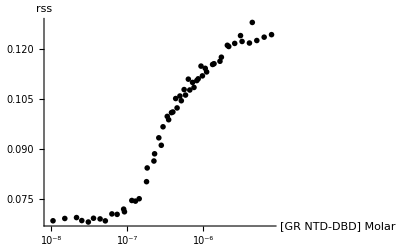

```mathematica
ListLogLinearPlot[{FullMarch31A,FullMarch31C3},PlotRange->All,AxesLabel->{"[GR NTD-DBD] Molar","rss"}, PlotTheme->"Monochrome"]
```

### April 1st 2017; HALF GRE

```mathematica
SetDirectory["~/Documents/My_Research/Hilser_Lab/Steady State Anisotropy/20170401_a_c3_greHalf"]
```

/Users/jordanwhite/Documents/My_Research/Hilser_Lab/Steady State Anisotropy/20170401_a_c3_greHalf

```mathematica
dataA=Drop[Import["20170401_ADBD_GRE.csv"],1];(*First column is 524nm, then 520nm, 516nm, 512nm, nanoMolar concentration of ADBD*)
```

```mathematica
datac3=Drop[Import["20170401_C3DBD_GRE.csv"],1];(*First column is 524nm, then 520nm, 516nm, 512nm, nanoMolar concentration of C3DBD*)
```

```mathematica
nm524A=Take[Transpose[dataA],1];
nm520A=Take[Transpose[dataA],{2}];
nm516A=Take[Transpose[dataA],{3}];
nm512A=Take[Transpose[dataA],{4}];
concA=N[Flatten[Take[Transpose[dataA]*10^-9,{5}]]];
data524A=Transpose[{Flatten[concA],Flatten[nm524A]}];
data520A=Transpose[{Flatten[concA],Flatten[nm520A]}];
data516A=Transpose[{Flatten[concA],Flatten[nm516A]}];
data512A=Transpose[{Flatten[concA],Flatten[nm512A]}];
```

```mathematica
nm524c3=Take[Transpose[datac3],1];
nm520c3=Take[Transpose[datac3],{2}];
nm516c3=Take[Transpose[datac3],{3}];
nm512c3=Take[Transpose[datac3],{4}];
concC3=N[Flatten[Take[Transpose[datac3]*10^-9,{5}]]];
data524c3=Transpose[{Flatten[concC3],Flatten[nm524c3]}];
data520c3=Transpose[{Flatten[concC3],Flatten[nm520c3]}];
data516c3=Transpose[{Flatten[concC3],Flatten[nm516c3]}];
data512c3=Transpose[{Flatten[concC3],Flatten[nm512c3]}];
```

```mathematica
HalfApril1A=Drop[Transpose[{Flatten[concA],Flatten[Mean[{nm512A,nm516A,nm520A,nm524A}]]}],-3];(*Crazy bound baseline shifts that I cut out here. Big Drop.*)
HalfApril1C3=Transpose[{Flatten[concC3],Flatten[Mean[{nm512c3,nm516c3,nm520c3,nm524c3}]]}];
```

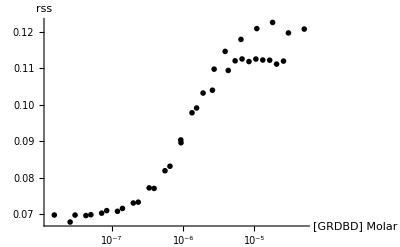

```mathematica
ListLogLinearPlot[{HalfApril1A,HalfApril1C3},PlotRange->All,AxesLabel->{"[GRDBD] Molar","rss"}, PlotTheme->"Monochrome"]
```

### April 2, 2017; FULL GRE

```mathematica
SetDirectory["~/Documents/My_Research/Hilser_Lab/Steady State Anisotropy/20170402_a_c3_gre"]
```

/Users/jordanwhite/Documents/My_Research/Hilser_Lab/Steady State Anisotropy/20170402_a_c3_gre

```mathematica
dataA=Drop[Import["20170402_ADBD_GRE.csv"],1];(*First column is 524nm, then 520nm, 516nm, 512nm, nanoMolar concentration of ADBD*)
```

```mathematica
datac3=Drop[Import["20170402_C3DBD_GRE.csv"],1];(*First column is 524nm, then 520nm, 516nm, 512nm, nanoMolar concentration of C3DBD*)
```

```mathematica
nm524A=Take[Transpose[dataA],1];
nm520A=Take[Transpose[dataA],{2}];
nm516A=Take[Transpose[dataA],{3}];
nm512A=Take[Transpose[dataA],{4}];
concA=N[Flatten[Take[Transpose[dataA]*10^-9,{5}]]];
data524A=Transpose[{Flatten[concA],Flatten[nm524A]}];
data520A=Transpose[{Flatten[concA],Flatten[nm520A]}];
data516A=Transpose[{Flatten[concA],Flatten[nm516A]}];
data512A=Transpose[{Flatten[concA],Flatten[nm512A]}];
```

```mathematica
nm524c3=Take[Transpose[datac3],1];
nm520c3=Take[Transpose[datac3],{2}];
nm516c3=Take[Transpose[datac3],{3}];
nm512c3=Take[Transpose[datac3],{4}];
concC3=N[Flatten[Take[Transpose[datac3]*10^-9,{5}]]];
data524c3=Transpose[{Flatten[concC3],Flatten[nm524c3]}];
data520c3=Transpose[{Flatten[concC3],Flatten[nm520c3]}];
data516c3=Transpose[{Flatten[concC3],Flatten[nm516c3]}];
data512c3=Transpose[{Flatten[concC3],Flatten[nm512c3]}];
```

```mathematica
FullApril2A=Transpose[{Flatten[concA],Flatten[Mean[{nm512A,nm516A,nm520A,nm524A}]]}];
FullApril2C3=Drop[Transpose[{Flatten[concC3],Flatten[Mean[{nm512c3,nm516c3,nm520c3,nm524c3}]]}],-1];
```

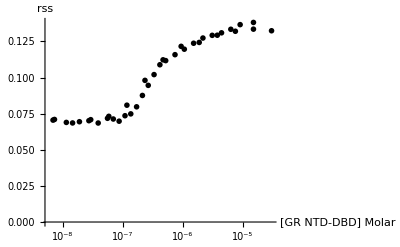

```mathematica
ListLogLinearPlot[{FullApril2A,FullApril2C3},PlotRange->All,AxesLabel->{"[GR NTD-DBD] Molar","rss"}, PlotTheme->"Monochrome"]
```

### April 3, 2017; HALF GRE

```mathematica
SetDirectory["~/Documents/My_Research/Hilser_Lab/Steady State Anisotropy/20170403_a_c3_greHalf"]
```

/Users/jordanwhite/Documents/My_Research/Hilser_Lab/Steady State Anisotropy/20170403_a_c3_greHalf

```mathematica
dataA=Drop[Import["20170403_ADBD_GREhalf.csv"],1];(*First column is 524nm, then 520nm, 516nm, 512nm, nanoMolar concentration of ADBD*)
```

```mathematica
datac3=Drop[Import["20170403_C3DBD_GREhalf.csv"],1];(*First column is 524nm, then 520nm, 516nm, 512nm, nanoMolar concentration of C3DBD*)
```

```mathematica
nm524A=Take[Transpose[dataA],1];
nm520A=Take[Transpose[dataA],{2}];
nm516A=Take[Transpose[dataA],{3}];
nm512A=Take[Transpose[dataA],{4}];
concA=N[Flatten[Take[Transpose[dataA]*10^-9,{5}]]];
data524A=Transpose[{Flatten[concA],Flatten[nm524A]}];
data520A=Transpose[{Flatten[concA],Flatten[nm520A]}];
data516A=Transpose[{Flatten[concA],Flatten[nm516A]}];
data512A=Transpose[{Flatten[concA],Flatten[nm512A]}];
```

```mathematica
nm524c3=Take[Transpose[datac3],1];
nm520c3=Take[Transpose[datac3],{2}];
nm516c3=Take[Transpose[datac3],{3}];
nm512c3=Take[Transpose[datac3],{4}];
concC3=N[Flatten[Take[Transpose[datac3]*10^-9,{5}]]];
data524c3=Transpose[{Flatten[concC3],Flatten[nm524c3]}];
data520c3=Transpose[{Flatten[concC3],Flatten[nm520c3]}];
data516c3=Transpose[{Flatten[concC3],Flatten[nm516c3]}];
data512c3=Transpose[{Flatten[concC3],Flatten[nm512c3]}];
```

```mathematica
HalfApril3A=Drop[Transpose[{Flatten[concA],Flatten[Mean[{nm512A,nm516A,nm520A,nm524A}]]}],-3];
HalfApril3C3=Transpose[{Flatten[concC3],Flatten[Mean[{nm512c3,nm516c3,nm520c3,nm524c3}]]}];
```

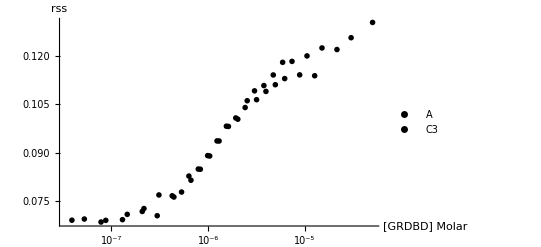

```mathematica
ListLogLinearPlot[{HalfApril3A,HalfApril3C3},PlotRange->All,AxesLabel->{"[GRDBD] Molar","rss"}, PlotTheme->"Monochrome",PlotLegends->{"A","C3"}]
```

### April 17, 2017; Full GRE +/- TSG101cc 100 µM, ADBD (C3DBD data had odd non-cooperativity and may have been oxidized)

```mathematica
SetDirectory["~/Documents/My_Research/Hilser_Lab/Steady State Anisotropy/20170417_a_c3OX?_gre_tsg"]
```

/Users/jordanwhite/Documents/My_Research/Hilser_Lab/Steady State Anisotropy/20170417_a_c3OX?_gre_tsg

```mathematica
dataA=Drop[Import["20170417_ADBD_GRE.csv"],1];(*First column is 524nm, then 520nm, 516nm, 512nm, nanoMolar concentration of ADBD*)
```

```mathematica
nm524A=Take[Transpose[dataA],1];
nm520A=Take[Transpose[dataA],{2}];
nm516A=Take[Transpose[dataA],{3}];
nm512A=Take[Transpose[dataA],{4}];
concA=N[Flatten[Take[Transpose[dataA]*10^-9,{5}]]];
data524A=Transpose[{Flatten[concA],Flatten[nm524A]}];
data520A=Transpose[{Flatten[concA],Flatten[nm520A]}];
data516A=Transpose[{Flatten[concA],Flatten[nm516A]}];
data512A=Transpose[{Flatten[concA],Flatten[nm512A]}];
```

```mathematica
FullApril17A=Drop[Transpose[{Flatten[concA],Flatten[Mean[{nm512A,nm516A,nm520A,nm524A}]]}],-2];
```

```mathematica
dataA=Drop[Import["20170417_ADBD_GRE_TSG.csv"],1];(*First column is 524nm, then 520nm, 516nm, 512nm, nanoMolar concentration of ADBD*)
```

```mathematica
nm524A=Take[Transpose[dataA],1];
nm520A=Take[Transpose[dataA],{2}];
nm516A=Take[Transpose[dataA],{3}];
nm512A=Take[Transpose[dataA],{4}];
concA=N[Flatten[Take[Transpose[dataA]*10^-9,{5}]]];
data524A=Transpose[{Flatten[concA],Flatten[nm524A]}];
data520A=Transpose[{Flatten[concA],Flatten[nm520A]}];
data516A=Transpose[{Flatten[concA],Flatten[nm516A]}];
data512A=Transpose[{Flatten[concA],Flatten[nm512A]}];
```

```mathematica
FullTSGApril17A=Transpose[{Flatten[concA],Flatten[Mean[{nm512A,nm516A,nm520A,nm524A}]]}];
```

### May 7, 2017; FULL GRE + TSG101cc 100 µM

```mathematica
SetDirectory["~/Documents/My_Research/Hilser_Lab/Steady State Anisotropy/20170507_GRE_GRdbd_tsg"]
```

/Users/jordanwhite/Documents/My_Research/Hilser_Lab/Steady State Anisotropy/20170507_GRE_GRdbd_tsg

```mathematica
datac3=Drop[Import["20170507_C3DBD_GRE_TSG.csv"],1];(*First column is 524nm, then 520nm, 516nm, 512nm, nanoMolar concentration of C3DBD*)
```

```mathematica
nm524c3=Take[Transpose[datac3],1];
nm520c3=Take[Transpose[datac3],{2}];
nm516c3=Take[Transpose[datac3],{3}];
nm512c3=Take[Transpose[datac3],{4}];
concC3=N[Flatten[Take[Transpose[datac3]*10^-9,{5}]]];
data524c3=Transpose[{Flatten[concC3],Flatten[nm524c3]}];
data520c3=Transpose[{Flatten[concC3],Flatten[nm520c3]}];
data516c3=Transpose[{Flatten[concC3],Flatten[nm516c3]}];
data512c3=Transpose[{Flatten[concC3],Flatten[nm512c3]}];
```

```mathematica
FullTSGccMay7C3=Transpose[{Flatten[concC3],Flatten[Mean[{nm512c3,nm516c3,nm520c3,nm524c3}]]}];
```

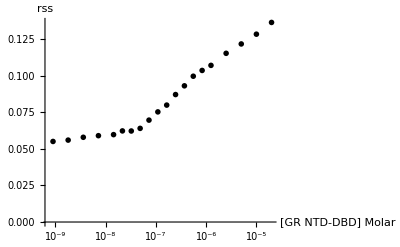

```mathematica
ListLogLinearPlot[FullTSGccMay7C3,PlotRange->All,AxesLabel->{"[GR NTD-DBD] Molar","rss"}, PlotTheme->"Monochrome"]
```

### May 8, 2017; Half and Full GRE +/- TSG101cc 100µM

```mathematica
SetDirectory["~/Documents/My_Research/Hilser_Lab/Steady State Anisotropy/20170508_C3dbd"]
```

/Users/jordanwhite/Documents/My_Research/Hilser_Lab/Steady State Anisotropy/20170508_C3dbd

```mathematica
datac3full=Drop[Import["20170508_C3DBD_GRE.csv"],1];(*First column is 524nm, then 520nm, 516nm, 512nm, nanoMolar concentration of C3DBD*)
```

```mathematica
nm524c3full=Take[Transpose[datac3full],1];
nm520c3full=Take[Transpose[datac3full],{2}];
nm516c3full=Take[Transpose[datac3full],{3}];
nm512c3full=Take[Transpose[datac3full],{4}];
concC3full=N[Flatten[Take[Transpose[datac3full]*10^-9,{5}]]];
data524c3full=Transpose[{Flatten[concC3full],Flatten[nm524c3full]}];
data520c3full=Transpose[{Flatten[concC3full],Flatten[nm520c3full]}];
data516c3full=Transpose[{Flatten[concC3full],Flatten[nm516c3full]}];
data512c3full=Transpose[{Flatten[concC3full],Flatten[nm512c3full]}];
FullMay8C3=Transpose[{Flatten[concC3full],Flatten[Mean[{nm512c3full,nm516c3full,nm520c3full,nm524c3full}]]}];
```

```mathematica
datac3half=Drop[Import["20170508_C3DBD_GREhalf.csv"],1];(*First column is 524nm, then 520nm, 516nm, 512nm, nanoMolar concentration of C3DBD*)
```

```mathematica
nm524c3half=Take[Transpose[datac3half],1];
nm520c3half=Take[Transpose[datac3half],{2}];
nm516c3half=Take[Transpose[datac3half],{3}];
nm512c3half=Take[Transpose[datac3half],{4}];
concC3half=N[Flatten[Take[Transpose[datac3half]*10^-9,{5}]]];
data524c3half=Transpose[{Flatten[concC3half],Flatten[nm524c3half]}];
data520c3half=Transpose[{Flatten[concC3half],Flatten[nm520c3half]}];
data516c3half=Transpose[{Flatten[concC3half],Flatten[nm516c3half]}];
data512c3half=Transpose[{Flatten[concC3half],Flatten[nm512c3half]}];
```

```mathematica
datac3halfTSG=Drop[Import["20170508_C3DBD_GREhalf_TSG.csv"],1];(*First column is 524nm, then 520nm, 516nm, 512nm, nanoMolar concentration of C3DBD*)
```

```mathematica
nm524c3halfTSG=Take[Transpose[datac3halfTSG],1];
nm520c3halfTSG=Take[Transpose[datac3halfTSG],{2}];
nm516c3halfTSG=Take[Transpose[datac3halfTSG],{3}];
nm512c3halfTSG=Take[Transpose[datac3halfTSG],{4}];
concC3halfTSG=N[Flatten[Take[Transpose[datac3halfTSG]*10^-9,{5}]]];
data524c3halfTSG=Transpose[{Flatten[concC3halfTSG],Flatten[nm524c3halfTSG]}];
data520c3halfTSG=Transpose[{Flatten[concC3halfTSG],Flatten[nm520c3halfTSG]}];
data516c3halfTSG=Transpose[{Flatten[concC3halfTSG],Flatten[nm516c3halfTSG]}];
data512c3halfTSG=Transpose[{Flatten[concC3halfTSG],Flatten[nm512c3halfTSG]}];
```

```mathematica
HalfMay8C3=Transpose[{Flatten[concC3half],Flatten[Mean[{nm512c3half,nm516c3half,nm520c3half,nm524c3half}]]}];
HalfTSGccMay8C3=Transpose[{Flatten[concC3halfTSG],Flatten[Mean[{nm512c3halfTSG,nm516c3halfTSG,nm520c3halfTSG,nm524c3halfTSG}]]}];
```

### May 26, 2017; C3 + halfGRE ± 100 µM TSG; A+GRE+100µM TSG

```mathematica
SetDirectory["~/Documents/My_Research/Hilser_Lab/Steady State Anisotropy/20170526_GR_GRE_TSG"]
```

/Users/jordanwhite/Documents/My_Research/Hilser_Lab/Steady State Anisotropy/20170526_GR_GRE_TSG

```mathematica
datac3half=Drop[Import["20170526_C3DBD_GREhalf.csv"],1];(*First column is 524nm, then 520nm, 516nm, 512nm, nanoMolar concentration of C3DBD*)
```

```mathematica
nm524c3half=Take[Transpose[datac3half],1];
nm520c3half=Take[Transpose[datac3half],{2}];
nm516c3half=Take[Transpose[datac3half],{3}];
nm512c3half=Take[Transpose[datac3half],{4}];
concC3half=N[Flatten[Take[Transpose[datac3half]*10^-9,{5}]]];
data524c3half=Transpose[{Flatten[concC3half],Flatten[nm524c3half]}];
data520c3half=Transpose[{Flatten[concC3half],Flatten[nm520c3half]}];
data516c3half=Transpose[{Flatten[concC3half],Flatten[nm516c3half]}];
data512c3half=Transpose[{Flatten[concC3half],Flatten[nm512c3half]}];
```

```mathematica
datac3halfTSG=Drop[Import["20170526_C3DBD_GREhalf_tsg.csv"],1];(*First column is 524nm, then 520nm, 516nm, 512nm, nanoMolar concentration of C3DBD*)
```

```mathematica
nm524c3halfTSG=Take[Transpose[datac3halfTSG],1];
nm520c3halfTSG=Take[Transpose[datac3halfTSG],{2}];
nm516c3halfTSG=Take[Transpose[datac3halfTSG],{3}];
nm512c3halfTSG=Take[Transpose[datac3halfTSG],{4}];
concC3halfTSG=N[Flatten[Take[Transpose[datac3halfTSG]*10^-9,{5}]]];
data524c3halfTSG=Transpose[{Flatten[concC3halfTSG],Flatten[nm524c3halfTSG]}];
data520c3halfTSG=Transpose[{Flatten[concC3halfTSG],Flatten[nm520c3halfTSG]}];
data516c3halfTSG=Transpose[{Flatten[concC3halfTSG],Flatten[nm516c3halfTSG]}];
data512c3halfTSG=Transpose[{Flatten[concC3halfTSG],Flatten[nm512c3halfTSG]}];
```

```mathematica
dataA=Drop[Import["20170526_ADBD_GRE_tsg.csv"],1];(*First column is 524nm, then 520nm, 516nm, 512nm, nanoMolar concentration of ADBD*)
```

```mathematica
nm524A=Take[Transpose[dataA],1];
nm520A=Take[Transpose[dataA],{2}];
nm516A=Take[Transpose[dataA],{3}];
nm512A=Take[Transpose[dataA],{4}];
concA=N[Flatten[Take[Transpose[dataA]*10^-9,{5}]]];
data524A=Transpose[{Flatten[concA],Flatten[nm524A]}];
data520A=Transpose[{Flatten[concA],Flatten[nm520A]}];
data516A=Transpose[{Flatten[concA],Flatten[nm516A]}];
data512A=Transpose[{Flatten[concA],Flatten[nm512A]}];
```

```mathematica
HalfMay26C3=Transpose[{Flatten[concC3half],Flatten[Mean[{nm512c3half,nm516c3half,nm520c3half,nm524c3half}]]}];
HalfTSGccMay26C3=Transpose[{Flatten[concC3halfTSG],Flatten[Mean[{nm512c3halfTSG,nm516c3halfTSG,nm520c3halfTSG,nm524c3halfTSG}]]}];
Full2017May26A100=Drop[Transpose[{Flatten[concA],Flatten[Mean[{nm512A,nm516A,nm520A,nm524A}]]}],1];(* First data point has wierdly high anisotropy. Probably light scatter from an air bubble that I missed *)
```

### May 27, 2017; ADBD + full-GRE w/out TSG and +half-site w/TSG 100 µM

```mathematica
SetDirectory["~/Documents/My_Research/Hilser_Lab/Steady State Anisotropy/20170527_GR_gre_tsg"]
```

/Users/jordanwhite/Documents/My_Research/Hilser_Lab/Steady State Anisotropy/20170527_GR_gre_tsg

```mathematica
dataAfull=Drop[Import["20170527_ADBD_GRE.csv"],1];(*First column is 524nm, then 520nm, 516nm, 512nm, nanoMolar concentration of C3DBD*)
```

```mathematica
nm524Afull=Take[Transpose[dataAfull],1];
nm520Afull=Take[Transpose[dataAfull],{2}];
nm516Afull=Take[Transpose[dataAfull],{3}];
nm512Afull=Take[Transpose[dataAfull],{4}];
concAfull=N[Flatten[Take[Transpose[dataAfull]*10^-9,{5}]]];
data524Afull=Transpose[{Flatten[concAfull],Flatten[nm524Afull]}];
data520Afull=Transpose[{Flatten[concAfull],Flatten[nm520Afull]}];
data516Afull=Transpose[{Flatten[concAfull],Flatten[nm516Afull]}];
data512Afull=Transpose[{Flatten[concAfull],Flatten[nm512Afull]}];
```

```mathematica
dataAhalfTSG=Drop[Import["20170527_ADBD_halfGRE_tsg.csv"],1];(*First column is 524nm, then 520nm, 516nm, 512nm, nanoMolar concentration of C3DBD*)
```

```mathematica
nm524AhalfTSG=Take[Transpose[dataAhalfTSG],1];
nm520AhalfTSG=Take[Transpose[dataAhalfTSG],{2}];
nm516AhalfTSG=Take[Transpose[dataAhalfTSG],{3}];
nm512AhalfTSG=Take[Transpose[dataAhalfTSG],{4}];
concAhalfTSG=N[Flatten[Take[Transpose[dataAhalfTSG]*10^-9,{5}]]];
data524AhalfTSG=Transpose[{Flatten[concAhalfTSG],Flatten[nm524AhalfTSG]}];
data520AhalfTSG=Transpose[{Flatten[concAhalfTSG],Flatten[nm520AhalfTSG]}];
data516AhalfTSG=Transpose[{Flatten[concAhalfTSG],Flatten[nm516AhalfTSG]}];
data512AhalfTSG=Transpose[{Flatten[concAhalfTSG],Flatten[nm512AhalfTSG]}];
```

```mathematica
FullMay27A=Transpose[{Flatten[concAfull],Flatten[Mean[{nm512Afull,nm516Afull,nm520Afull,nm524Afull}]]}];
```

```mathematica
HalfTSGMay27A=Drop[Transpose[{Flatten[concAhalfTSG],Flatten[Mean[{nm512AhalfTSG,nm516AhalfTSG,nm520AhalfTSG,nm524AhalfTSG}]]}],-1]; (* Wierd spike on first datapoint *)
```

### June 17, 2017; ADBD + half-site w/or w/out TSG and +full GRE w/TSG 100 µM

```mathematica
SetDirectory["~/Documents/My_Research/Hilser_Lab/Steady State Anisotropy/20170617_Adbd"]
```

/Users/jordanwhite/Documents/My_Research/Hilser_Lab/Steady State Anisotropy/20170617_Adbd

```mathematica
dataAfulltsg=Drop[Import["20170617_ADBD_fullGRE_TSG.csv"],1];(*First column is 524nm, then 520nm, 516nm, 512nm, nanoMolar concentration of C3DBD*)
```

```mathematica
nm524Afulltsg=Take[Transpose[dataAfulltsg],1];
nm520Afulltsg=Take[Transpose[dataAfulltsg],{2}];
nm516Afulltsg=Take[Transpose[dataAfulltsg],{3}];
nm512Afulltsg=Take[Transpose[dataAfulltsg],{4}];
concAfulltsg=N[Flatten[Take[Transpose[dataAfulltsg]*10^-9,{5}]]];
data524Afulltsg=Transpose[{Flatten[concAfulltsg],Flatten[nm524Afulltsg]}];
data520Afulltsg=Transpose[{Flatten[concAfulltsg],Flatten[nm520Afulltsg]}];
data516Afulltsg=Transpose[{Flatten[concAfulltsg],Flatten[nm516Afulltsg]}];
data512Afulltsg=Transpose[{Flatten[concAfulltsg],Flatten[nm512Afulltsg]}];
```

```mathematica
dataAhalfTSG=Drop[Import["20170617_ADBD_halfGRE_tsg.csv"],1];(*First column is 524nm, then 520nm, 516nm, 512nm, nanoMolar concentration of C3DBD*)
```

```mathematica
nm524AhalfTSG=Take[Transpose[dataAhalfTSG],1];
nm520AhalfTSG=Take[Transpose[dataAhalfTSG],{2}];
nm516AhalfTSG=Take[Transpose[dataAhalfTSG],{3}];
nm512AhalfTSG=Take[Transpose[dataAhalfTSG],{4}];
concAhalfTSG=N[Flatten[Take[Transpose[dataAhalfTSG]*10^-9,{5}]]];
data524AhalfTSG=Transpose[{Flatten[concAhalfTSG],Flatten[nm524AhalfTSG]}];
data520AhalfTSG=Transpose[{Flatten[concAhalfTSG],Flatten[nm520AhalfTSG]}];
data516AhalfTSG=Transpose[{Flatten[concAhalfTSG],Flatten[nm516AhalfTSG]}];
data512AhalfTSG=Transpose[{Flatten[concAhalfTSG],Flatten[nm512AhalfTSG]}];
```

```mathematica
dataAhalf=Drop[Import["20170617_ADBD_halfGRE.csv"],1];(*First column is 524nm, then 520nm, 516nm, 512nm, nanoMolar concentration of C3DBD*)
```

```mathematica
nm524Ahalf=Take[Transpose[dataAhalf],1];
nm520Ahalf=Take[Transpose[dataAhalf],{2}];
nm516Ahalf=Take[Transpose[dataAhalf],{3}];
nm512Ahalf=Take[Transpose[dataAhalf],{4}];
concAhalf=N[Flatten[Take[Transpose[dataAhalf]*10^-9,{5}]]];
data524Ahalf=Transpose[{Flatten[concAhalf],Flatten[nm524Ahalf]}];
data520Ahalf=Transpose[{Flatten[concAhalf],Flatten[nm520Ahalf]}];
data516Ahalf=Transpose[{Flatten[concAhalf],Flatten[nm516Ahalf]}];
data512Ahalf=Transpose[{Flatten[concAhalf],Flatten[nm512Ahalf]}];
```

```mathematica
FullTSGJune17A=Transpose[{Flatten[concAfulltsg],Flatten[Mean[{nm512Afulltsg,nm516Afulltsg,nm520Afulltsg,nm524Afulltsg}]]}];
```

```mathematica
HalfTSGJune17A=Transpose[{Flatten[concAhalfTSG],Flatten[Mean[{nm512AhalfTSG,nm516AhalfTSG,nm520AhalfTSG,nm524AhalfTSG}]]}];
```

```mathematica
HalfJune17A=Drop[Transpose[{Flatten[concAhalf],Flatten[Mean[{nm512Ahalf,nm516Ahalf,nm520Ahalf,nm524Ahalf}]]}],-2];(*First two points look odd*)
```

### 2018 January 26; A/C3 + GRE + 20 or 200 µM TSG101cc

```mathematica
SetDirectory["~/Documents/My_Research/Hilser_Lab/Steady State Anisotropy/20180126"]
```

/Users/jordanwhite/Documents/My_Research/Hilser_Lab/Steady State Anisotropy/20180126

```mathematica
dataC320=Drop[Import["20180126_C3DBD_20µMTSG101cc_fullGRE.csv"],1];(*First column is 524nm, then 520nm, 516nm, 512nm, nM*)
```

```mathematica
nm524C320=Take[Transpose[dataC320],1];
nm520C320=Take[Transpose[dataC320],{2}];
nm516C320=Take[Transpose[dataC320],{3}];
nm512C320=Take[Transpose[dataC320],{4}];
concC320=N[Flatten[Take[Transpose[dataC320]*10^-9,{5}]]];
```

```mathematica
Full2018Jan26C320=Transpose[{Flatten[concC320],Flatten[Mean[{nm512C320,nm516C320,nm520C320,nm524C320}]]}];
```

```mathematica
dataA20=Drop[Import["20180126_ADBD-20µMTSG101cc-fullGRE.csv"],1];(*First column is 524nm, then 520nm, 516nm, 512nm, nM*)
```

```mathematica
nm524A20=Take[Transpose[dataA20],1];
nm520A20=Take[Transpose[dataA20],{2}];
nm516A20=Take[Transpose[dataA20],{3}];
nm512A20=Take[Transpose[dataA20],{4}];
concA20=N[Flatten[Take[Transpose[dataA20]*10^-9,{5}]]];
```

```mathematica
Full2018Jan26A20=Transpose[{Flatten[concA20],Flatten[Mean[{nm512A20,nm516A20,nm520A20,nm524A20}]]}];
```

```mathematica
dataA200=Drop[Import["20180126_ADBD-200µMTSG101cc-fullGRE.csv"],1];(*First column is 524nm, then 520nm, 516nm, 512nm, nM*)
```

```mathematica
nm524A200=Take[Transpose[dataA200],1];
nm520A200=Take[Transpose[dataA200],{2}];
nm516A200=Take[Transpose[dataA200],{3}];
nm512A200=Take[Transpose[dataA200],{4}];
concA200=N[Flatten[Take[Transpose[dataA200]*10^-9,{5}]]];
```

```mathematica
Full2018Jan26A200=Transpose[{Flatten[concA200],Flatten[Mean[{nm512A200,nm516A200,nm520A200,nm524A200}]]}];
```

```mathematica
dataC3200=Drop[Import["20180126_C3DBD-200µMTSG101cc-fullGRE.csv"],1];(*First column is 524nm, then 520nm, 516nm, 512nm, nM*)
```

```mathematica
nm524C3200=Take[Transpose[dataC3200],1];
nm520C3200=Take[Transpose[dataC3200],{2}];
nm516C3200=Take[Transpose[dataC3200],{3}];
nm512C3200=Take[Transpose[dataC3200],{4}];
concC3200=N[Flatten[Take[Transpose[dataC3200]*10^-9,{5}]]];
```

```mathematica
Full2018Jan26C3200=Transpose[{Flatten[concC3200],Flatten[Mean[{nm512C3200,nm516C3200,nm520C3200,nm524C3200}]]}];
```

### 2018 February 15; A/C3 + GRE + 20 or 200 µM TSG101cc

```mathematica
SetDirectory["~/Documents/My_Research/Hilser_Lab/Steady State Anisotropy/20180215"]
```

/Users/jordanwhite/Documents/My_Research/Hilser_Lab/Steady State Anisotropy/20180215

```mathematica
dataC320=Drop[Import["20180215_C3DBD-20µMTSG101cc-GRE.csv"],1];(*First column is 524nm, then 520nm, 516nm, 512nm, nM*)
```

```mathematica
nm524C320=Take[Transpose[dataC320],1];
nm520C320=Take[Transpose[dataC320],{2}];
nm516C320=Take[Transpose[dataC320],{3}];
nm512C320=Take[Transpose[dataC320],{4}];
concC320=N[Flatten[Take[Transpose[dataC320]*10^-9,{5}]]];
```

```mathematica
Full2018Feb15C320=Drop[Transpose[{Flatten[concC320],Flatten[Mean[{nm512C320,nm516C320,nm520C320,nm524C320}]]}],1];
```

```mathematica
dataA20=Drop[Import["20180215_ADBD-20µMTSG101cc-GRE.csv"],1];(*First column is 524nm, then 520nm, 516nm, 512nm, nM*)
```

```mathematica
nm524A20=Take[Transpose[dataA20],1];
nm520A20=Take[Transpose[dataA20],{2}];
nm516A20=Take[Transpose[dataA20],{3}];
nm512A20=Take[Transpose[dataA20],{4}];
concA20=N[Flatten[Take[Transpose[dataA20]*10^-9,{5}]]];
```

```mathematica
Full2018Feb15A20=Transpose[{Flatten[concA20],Flatten[Mean[{nm512A20,nm516A20,nm520A20,nm524A20}]]}];
```

```mathematica
dataA200=Drop[Import["20180215_ADBD-200µMTSG101cc-GRE.csv"],1];(*First column is 524nm, then 520nm, 516nm, 512nm, nM*)
```

```mathematica
nm524A200=Take[Transpose[dataA200],1];
nm520A200=Take[Transpose[dataA200],{2}];
nm516A200=Take[Transpose[dataA200],{3}];
nm512A200=Take[Transpose[dataA200],{4}];
concA200=N[Flatten[Take[Transpose[dataA200]*10^-9,{5}]]];
```

```mathematica
Full2018Feb15A200=Transpose[{Flatten[concA200],Flatten[Mean[{nm512A200,nm516A200,nm520A200,nm524A200}]]}];
```

```mathematica
dataC3200=Drop[Import["20180215_C3DBD-200µMTSG101cc-GRE.csv"],1];(*First column is 524nm, then 520nm, 516nm, 512nm, nM*)
```

```mathematica
nm524C3200=Take[Transpose[dataC3200],1];
nm520C3200=Take[Transpose[dataC3200],{2}];
nm516C3200=Take[Transpose[dataC3200],{3}];
nm512C3200=Take[Transpose[dataC3200],{4}];
concC3200=N[Flatten[Take[Transpose[dataC3200]*10^-9,{5}]]];
```

```mathematica
Full2018Feb15C3200=Transpose[{Flatten[concC3200],Flatten[Mean[{nm512C3200,nm516C3200,nm520C3200,nm524C3200}]]}];
```

### March 1st, 2018; A/C3 + 2, 100 µM TSG101cc

```mathematica
SetDirectory["~/Documents/My_Research/Hilser_Lab/Steady State Anisotropy/20180301"]
```

/Users/jordanwhite/Documents/My_Research/Hilser_Lab/Steady State Anisotropy/20180301

```mathematica
dataA2=Drop[Import["20180301_ADBD-2µMTSG101cc-GRE.csv"],1];(*First column is 524nm, then 520nm, 516nm, 512nm, nM*)
nm524A2=Take[Transpose[dataA2],1];
nm520A2=Take[Transpose[dataA2],{2}];
nm516A2=Take[Transpose[dataA2],{3}];
nm512A2=Take[Transpose[dataA2],{4}];
concA2=N[Flatten[Take[Transpose[dataA2]*10^-9,{5}]]];
Full2018Mar01A2=Transpose[{Flatten[concA2],Flatten[Mean[{nm512A2,nm516A2,nm520A2,nm524A2}]]}];
```

```mathematica
dataC32=Drop[Import["20180301_C3DBD-2µMTSG101cc-GRE.csv"],1];(*First column is 524nm, then 520nm, 516nm, 512nm, nM*)
nm524C32=Take[Transpose[dataC32],1];
nm520C32=Take[Transpose[dataC32],{2}];
nm516C32=Take[Transpose[dataC32],{3}];
nm512C32=Take[Transpose[dataC32],{4}];
concC32=N[Flatten[Take[Transpose[dataC32]*10^-9,{5}]]];
Full2018Mar01C32=Transpose[{Flatten[concC32],Flatten[Mean[{nm512C32,nm516C32,nm520C32,nm524C32}]]}];
```

```mathematica
dataA100=Drop[Import["20180301_ADBD-100µMTSG101cc-GRE.csv"],1];(*First column is 524nm, then 520nm, 516nm, 512nm, nM*)
nm524A100=Take[Transpose[dataA100],1];
nm520A100=Take[Transpose[dataA100],{2}];
nm516A100=Take[Transpose[dataA100],{3}];
nm512A100=Take[Transpose[dataA100],{4}];
concA100=N[Flatten[Take[Transpose[dataA100]*10^-9,{5}]]];
Full2018Mar01A100=Transpose[{Flatten[concA100],Flatten[Mean[{nm512A100,nm516A100,nm520A100,nm524A100}]]}];
```

```mathematica
dataC3100=Drop[Import["20180301_C3DBD-100µMTSG101cc-GRE.csv"],1];(*First column is 524nm, then 520nm, 516nm, 512nm, nM*)
nm524C3100=Take[Transpose[dataC3100],1];
nm520C3100=Take[Transpose[dataC3100],{2}];
nm516C3100=Take[Transpose[dataC3100],{3}];
nm512C3100=Take[Transpose[dataC3100],{4}];
concC3100=N[Flatten[Take[Transpose[dataC3100]*10^-9,{5}]]];
Full2018Mar01C3100=Transpose[{Flatten[concC3100],Flatten[Mean[{nm512C3100,nm516C3100,nm520C3100,nm524C3100}]]}];
```

### 2018 March 8th; Several TSG101cc concentrations, full GRE

```mathematica
SetDirectory["~/Documents/My_Research/Hilser_Lab/Steady State Anisotropy/20180308"]
```

/Users/jordanwhite/Documents/My_Research/Hilser_Lab/Steady State Anisotropy/20180308

#### +0.2 µM TSG101cc

```mathematica
dataAo2=Drop[Import["20180308_ADBD-0.2µMTSG101cc-GRE.csv"],1];(*First column is 524nm, then 520nm, 516nm, 512nm, nM*)
```

```mathematica
nm524Ao2=Take[Transpose[dataAo2],1];
nm520Ao2=Take[Transpose[dataAo2],{2}];
nm516Ao2=Take[Transpose[dataAo2],{3}];
nm512Ao2=Take[Transpose[dataAo2],{4}];
concAo2=N[Flatten[Take[Transpose[dataAo2]*10^-9,{5}]]];
```

```mathematica
Full2018Mar08Ao2=Transpose[{Flatten[concAo2],Flatten[Mean[{nm512Ao2,nm516Ao2,nm520Ao2,nm524Ao2}]]}];
```

```mathematica
dataC3o2=Drop[Import["20180308_C3DBD-0.2µMTSG101cc-GRE.csv"],1];(*First column is 524nm, then 520nm, 516nm, 512nm, nM*)
```

```mathematica
nm524C3o2=Take[Transpose[dataC3o2],1];
nm520C3o2=Take[Transpose[dataC3o2],{2}];
nm516C3o2=Take[Transpose[dataC3o2],{3}];
nm512C3o2=Take[Transpose[dataC3o2],{4}];
concC3o2=N[Flatten[Take[Transpose[dataC3o2]*10^-9,{5}]]];
```

```mathematica
Full2018Mar08C3o2=Transpose[{Flatten[concC3o2],Flatten[Mean[{nm512C3o2,nm516C3o2,nm520C3o2,nm524C3o2}]]}];
```

#### +2 µM TSG101cc

```mathematica
dataA2=Drop[Import["20180308_ADBD-2µMTSG101cc-GRE.csv"],1];(*First column is 524nm, then 520nm, 516nm, 512nm, nM*)
```

```mathematica
nm524A2=Take[Transpose[dataA2],1];
nm520A2=Take[Transpose[dataA2],{2}];
nm516A2=Take[Transpose[dataA2],{3}];
nm512A2=Take[Transpose[dataA2],{4}];
concA2=N[Flatten[Take[Transpose[dataA2]*10^-9,{5}]]];
```

```mathematica
Full2018Mar08A2=Transpose[{Flatten[concA2],Flatten[Mean[{nm512A2,nm516A2,nm520A2,nm524A2}]]}];
```

```mathematica
dataC32=Drop[Import["20180308_C3DBD-2µMTSG101cc-GRE.csv"],1];(*First column is 524nm, then 520nm, 516nm, 512nm, nM*)
```

```mathematica
nm524C32=Take[Transpose[dataC32],1];
nm520C32=Take[Transpose[dataC32],{2}];
nm516C32=Take[Transpose[dataC32],{3}];
nm512C32=Take[Transpose[dataC32],{4}];
concC32=N[Flatten[Take[Transpose[dataC32]*10^-9,{5}]]];
```

```mathematica
Full2018Mar08C32=Transpose[{Flatten[concC32],Flatten[Mean[{nm512C32,nm516C32,nm520C32,nm524C32}]]}];
```

#### +100 µM TSG101cc

```mathematica
dataA100=Drop[Import["20180308_ADBD-100µMTSG101cc-GRE.csv"],1];(*First column is 524nm, then 520nm, 516nm, 512nm, nM*)
```

```mathematica
nm524A100=Take[Transpose[dataA100],1];
nm520A100=Take[Transpose[dataA100],{2}];
nm516A100=Take[Transpose[dataA100],{3}];
nm512A100=Take[Transpose[dataA100],{4}];
concA100=N[Flatten[Take[Transpose[dataA100]*10^-9,{5}]]];
```

```mathematica
Full2018Mar08A100=Transpose[{Flatten[concA100],Flatten[Mean[{nm512A100,nm516A100,nm520A100,nm524A100}]]}];
```

```mathematica
dataC3100=Drop[Import["20180308_C3DBD-100µMTSG101cc-GRE.csv"],1];(*First column is 524nm, then 520nm, 516nm, 512nm, nM*)
```

```mathematica
nm524C3100=Take[Transpose[dataC3100],1];
nm520C3100=Take[Transpose[dataC3100],{2}];
nm516C3100=Take[Transpose[dataC3100],{3}];
nm512C3100=Take[Transpose[dataC3100],{4}];
concC3100=N[Flatten[Take[Transpose[dataC3100]*10^-9,{5}]]];
```

```mathematica
Full2018Mar08C3100=Transpose[{Flatten[concC3100],Flatten[Mean[{nm512C3100,nm516C3100,nm520C3100,nm524C3100}]]}];
```

### March 9th, 2018; full GRE + 0.5 and 0.7 µM TSG101cc

```mathematica
SetDirectory["~/Documents/My_Research/Hilser_Lab/Steady State Anisotropy/20180309"]
```

/Users/jordanwhite/Documents/My_Research/Hilser_Lab/Steady State Anisotropy/20180309

```mathematica
dataAo4=Drop[Import["20180309_ADBD_0.4µMTSG101cc-GRE.csv"],1];(*First column is 524nm, then 520nm, 516nm, 512nm, nM*)
```

```mathematica
nm524Ao4=Take[Transpose[dataAo4],1];
nm520Ao4=Take[Transpose[dataAo4],{2}];
nm516Ao4=Take[Transpose[dataAo4],{3}];
nm512Ao4=Take[Transpose[dataAo4],{4}];
concAo4=N[Flatten[Take[Transpose[dataAo4]*10^-9,{5}]]];
```

```mathematica
Full2018Mar09Ao4=Transpose[{Flatten[concAo4],Flatten[Mean[{nm512Ao4,nm516Ao4,nm520Ao4,nm524Ao4}]]}];
```

```mathematica
dataC3o4=Drop[Import["20180309_C3DBD-0.4µMTSG101cc-GRE.csv"],1];(*First column is 524nm, then 520nm, 516nm, 512nm, nM*)
```

```mathematica
nm524C3o4=Take[Transpose[dataC3o4],1];
nm520C3o4=Take[Transpose[dataC3o4],{2}];
nm516C3o4=Take[Transpose[dataC3o4],{3}];
nm512C3o4=Take[Transpose[dataC3o4],{4}];
concC3o4=N[Flatten[Take[Transpose[dataC3o4]*10^-9,{5}]]];
```

```mathematica
Full2018Mar09C3o4=Transpose[{Flatten[concC3o4],Flatten[Mean[{nm512C3o4,nm516C3o4,nm520C3o4,nm524C3o4}]]}];
```

```mathematica
dataAo7=Drop[Import["20180309_ADBD_0.7µMTSG101cc-GRE.csv"],1];(*First column is 524nm, then 520nm, 516nm, 512nm, nM*)
```

```mathematica
nm524Ao7=Take[Transpose[dataAo7],1];
nm520Ao7=Take[Transpose[dataAo7],{2}];
nm516Ao7=Take[Transpose[dataAo7],{3}];
nm512Ao7=Take[Transpose[dataAo7],{4}];
concAo7=N[Flatten[Take[Transpose[dataAo7]*10^-9,{5}]]];
```

```mathematica
FullMar09Ao7=Transpose[{Flatten[concAo7],Flatten[Mean[{nm512Ao7,nm516Ao7,nm520Ao7,nm524Ao7}]]}];
```

```mathematica
dataC3o7=Drop[Import["20180309_C3DBD-0.7µMTSG101cc-GRE.csv"],1];(*First column is 524nm, then 520nm, 516nm, 512nm, nM*)
```

```mathematica
nm524C3o7=Take[Transpose[dataC3o7],1];
nm520C3o7=Take[Transpose[dataC3o7],{2}];
nm516C3o7=Take[Transpose[dataC3o7],{3}];
nm512C3o7=Take[Transpose[dataC3o7],{4}];
concC3o7=N[Flatten[Take[Transpose[dataC3o7]*10^-9,{5}]]];
```

```mathematica
Full2018Mar09C3o7=Transpose[{Flatten[concC3o7],Flatten[Mean[{nm512C3o7,nm516C3o7,nm520C3o7,nm524C3o7}]]}];
```

### May 4th 2018; C3 + 100 µM TSG101cc on the GRE half site

```mathematica
SetDirectory["~/Documents/My_Research/Hilser_Lab/Steady State Anisotropy/20180504"]
```

/Users/jordanwhite/Documents/My_Research/Hilser_Lab/Steady State Anisotropy/20180504

```mathematica
dataC3half=Drop[Import["20180504_C3DBD_halfGRE_100µMTSG101cc.csv"],1];(*First column is 524nm, then 520nm, 516nm, 512nm, nM*)
```

```mathematica
nm524C3half=Take[Transpose[dataC3half],1];
nm520C3half=Take[Transpose[dataC3half],{2}];
nm516C3half=Take[Transpose[dataC3half],{3}];
nm512C3half=Take[Transpose[dataC3half],{4}];
concC3half=N[Flatten[Take[Transpose[dataC3half]*10^-9,{5}]]];
```

```mathematica
HalfTSGMay042018C3=Drop[Transpose[{Flatten[concC3half],Flatten[Mean[{nm512C3half,nm516C3half,nm520C3half,nm524C3half}]]}],4];(*drop initial four points with odd baseline*)
```

### July 22, 2018; A + 100 µM TSG101cc on the GRE half-site

```mathematica
SetDirectory["~/Documents/My_Research/Hilser_Lab/Steady State Anisotropy/20180722"]
```

/Users/jordanwhite/Documents/My_Research/Hilser_Lab/Steady State Anisotropy/20180722

```mathematica
dataAhalf=Drop[Import["20180722_ADBD_halfGRE_100µMTSG101cc.csv"],1];(*First column is 524nm, then 520nm, 516nm, 512nm, nM*)
```

```mathematica
nm524Ahalf=Take[Transpose[dataAhalf],1];
nm520Ahalf=Take[Transpose[dataAhalf],{2}];
nm516Ahalf=Take[Transpose[dataAhalf],{3}];
nm512Ahalf=Take[Transpose[dataAhalf],{4}];
concAhalf=N[Flatten[Take[Transpose[dataAhalf]*10^-9,{5}]]];
```

```mathematica
HalfTSGJuly222018A=Transpose[{Flatten[concAhalf],Flatten[Mean[{nm512Ahalf,nm516Ahalf,nm520Ahalf,nm524Ahalf}]]}];
```

## Fit Full-GRE data without TSG:

March 31st, April 2nd, May 8th (C3 only on May 8th)

### Set up the models:

```mathematica
fullGREfitModelAmicro[gr_,GRE_,kd_,bb0_,mb0_,bu0_,mu0_,bb1_,mb1_,bu1_,mu1_,bb2_,mb2_,bu2_,mu2_,bb3_,mb3_,bu3_,mu3_,set_]:=Which[set==0,Evaluate@twoCoopMicro[gr,kd,bb0,mb0,bu0,mu0,GRE],
set==1,Evaluate@twoCoopMicro[gr,kd,bb1,mb1,bu1,mu1,GRE],
set==2,Evaluate@twoCoopMicro[gr,kd,bb2,mb2,bu2,mu2,GRE],
set==3,Evaluate@twoCoopMicro[gr,kd,bb3,mb3,bu3,mu3,GRE]];
fullGREfitModelC3micro[gr_,GRE_,kd_,bb0_,mb0_,bu0_,mu0_,bb1_,mb1_,bu1_,mu1_,bb2_,mb2_,bu2_,mu2_,set_]:=Which[set==0,Evaluate@twoCoopMicro[gr,kd,bb0,mb0,bu0,mu0,GRE],
set==1,Evaluate@twoCoopMicro[gr,kd,bb1,mb1,bu1,mu1,GRE],
set==2,Evaluate@twoCoopMicro[gr,kd,bb2,mb2,bu2,mu2,GRE]];
```

### Label the datasets:

```mathematica
globalFullA=Join[FullMarch31A/.{x_,y_}->{0,x,y},
FullApril2A/.{x_,y_}->{1,x,y},
FullApril17A/.{x_,y_}->{2,x,y},
FullMay27A/.{x_,y_}->{3,x,y}]; 
globalFullC3=Join[FullMarch31C3/.{x_,y_}->{0,x,y},
FullApril2C3/.{x_,y_}->{1,x,y},
FullMay8C3/.{x_,y_}->{2,x,y}];
```

Give log baselines only to the datasets that required it in their individual fits.

### NLM for A:

```mathematica
nlmFullAmicro=NonlinearModelFit[globalFullA,fullGREfitModelAmicro[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,0,bb2,0,bu2,0,bb3,mb3,bu3,0,set],{{kd,2*10^-7},{bb0,0.17019234012406864},{mb0,0.0037715448028710586},{bu0,0.06827558418500337},{bb1,0.17019234012406864},{mb1,0.0037715448028710586},{bu1,0.06827558418500337},{bb2,0.17019234012406864},{bu2,0.06827558418500337},{bb3,0.16},{mb3,0.001},{bu3,0.067}(*,{mu0,0.003},{mu1,0.003},{mu2,0.003}*)},{set,gr},MaxIterations->500]
```

FittedModel[Which[set==0,«6»,0.0947878 (1-100000000 (1/3 (1/100000000+gr)+(«1»)/(24 «1»)-1/6 (-1/(«24»)+«6»+«1»)^(1/3)))+100000000 «1» («1»)]]

{kd→2.12295×10^-7,bb0→0.172987,mb0→0.00408385,bu0→0.0678187,bb1→0.163063,mb1→0.00276632,bu1→0.0699493,bb2→0.120064,bu2→0.0690888,bb3→0.179471,mb3→0.00325025,bu3→0.0947878}

{5.99397×10^-9,0.00529832,0.000401183,0.000530602,0.00490149,0.00039459,0.00066677,0.000643075,0.000518693,0.00480098,0.000369989,0.000484104}

{{2.0034×10^-7,2.24249×10^-7},{0.16242,0.183554},{0.00328371,0.00488398},{0.0667605,0.068877},{0.153287,0.172839},{0.00197934,0.00355331},{0.0686195,0.0712791},{0.118782,0.121347},{0.0680543,0.0701233},{0.169896,0.189047},{0.00251233,0.00398817},{0.0938223,0.0957534}}

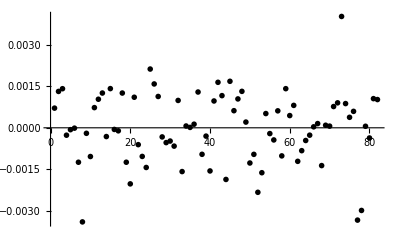

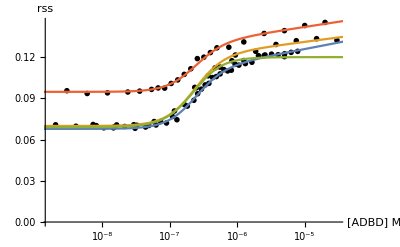

0.000130105

-1.19546×10^-8

```mathematica
nlmFullAmicro["BestFitParameters"]
nlmFullAmicro["ParameterErrors"]
nlmFullAmicro["ParameterConfidenceIntervals"]
ListPlot[nlmFullAmicro["FitResiduals"],PlotTheme->"Monochrome"]
Show[ListLogLinearPlot[{FullMarch31A,FullApril2A,FullApril17A,FullMay27A},PlotRange->All,AxesLabel->{"[ADBD] M","rss"}, PlotTheme->"Monochrome"],LogLinearPlot[{fullGREfitModelAmicro[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,0,bb2,0,bu2,0,bb3,mb3,bu3,0,0]/.nlmFullAmicro["BestFitParameters"],fullGREfitModelAmicro[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,0,bb2,0,bu2,0,bb3,mb3,bu3,0,1]/.nlmFullAmicro["BestFitParameters"],fullGREfitModelAmicro[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,0,bb2,0,bu2,0,bb3,mb3,bu3,0,2]/.nlmFullAmicro["BestFitParameters"],fullGREfitModelAmicro[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,0,bb2,0,bu2,0,bb3,mb3,bu3,0,3]/.nlmFullAmicro["BestFitParameters"]},{gr,10^-9,5*10^-5}]]
Total[nlmFullAmicro["FitResiduals"]^2]
nlmFullAmicro["ParameterErrors"][[1]]*y/.NMinimize[(0.975-CDF[StudentTDistribution[0
,1
,Length[nlmFullAmicro["Response"]]-12],x][[2]]/.{x->y})^2
,y][[2]](*95% Conf interval for Kd*)
```

### NLM for C3:

```mathematica
nlmFullC3micro=NonlinearModelFit[globalFullC3,fullGREfitModelC3micro[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,0,bb2,mb2,bu2,mu2,set],{{kd,2*10^-7},{bb0,0.17019234012406864},{mb0,0.0037715448028710586},{bu0,0.06827558418500337},{bb1,0.17019234012406864},{mb1,0.0037715448028710586},{bu1,0.06827558418500337},{bb2,0.17019234012406864},{mb2,0.0037715448028710586},{bu2,0.06827558418500337},{mu2,0.001}},{set,gr},MaxIterations->500]
```

FittedModel[Which[«1»]]

{kd→2.28549×10^-7,bb0→0.20831,mb0→0.00667596,bu0→0.0679305,bb1→0.203589,mb1→0.00583288,bu1→0.0679356,bb2→0.190589,mb2→0.00568312,bu2→0.0911366,mu2→0.00114334}

{1.18321×10^-8,0.0107605,0.000801723,0.000740713,0.0073076,0.000578747,0.000595666,0.0066967,0.000530211,0.00694748,0.00037947}

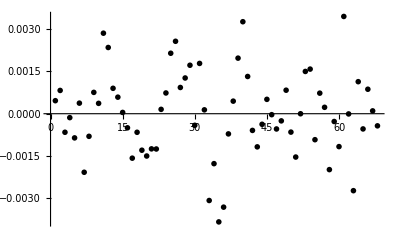

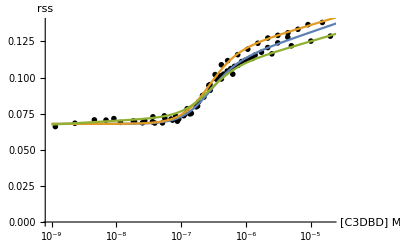

0.00014785

-2.36933×10^-8

```mathematica
nlmFullC3micro["BestFitParameters"]
nlmFullC3micro["ParameterErrors"]
ListPlot[nlmFullC3micro["FitResiduals"],PlotTheme->"Monochrome"]
Show[ListLogLinearPlot[{FullMarch31C3,FullApril2C3,FullMay8C3},PlotRange->All,AxesLabel->{"[C3DBD] M","rss"}, PlotTheme->"Monochrome"],LogLinearPlot[{fullGREfitModelC3micro[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,0,bb2,mb2,bu2,mu2,0]/.nlmFullC3micro["BestFitParameters"],fullGREfitModelC3micro[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,0,bb2,mb2,bu2,mu2,1]/.nlmFullC3micro["BestFitParameters"],fullGREfitModelC3micro[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,0,bb2,mb2,bu2,mu2,2]/.nlmFullC3micro["BestFitParameters"]},{gr,10^-9,5*10^-5}]]
Total[nlmFullC3micro["FitResiduals"]^2]
nlmFullC3micro["ParameterErrors"][[1]]*y/.NMinimize[(0.975-CDF[StudentTDistribution[0
,1
,Length[nlmFullC3micro["Response"]]-11],x][[2]]/.{x->y})^2
,y][[2]](*95% Conf interval for Kd*)
```

## Fit Full-GRE data with 0.2 µM TSG:

March 08

### Set up the models:

```mathematica
fullGRETSGo2fitModelAmicro[gr_,GRE_,kd_,bb0_,mb0_,bu0_,mu0_,bb1_,mb1_,bu1_,mu1_,set_]:=Which[set==0,Evaluate@twoCoopMicro[gr,kd,bb0,mb0,bu0,mu0,GRE],
set==1,Evaluate@twoCoopMicro[gr,kd,bb1,mb1,bu1,mu1,GRE]];
fullGRETSGo2fitModelC3micro[gr_,GRE_,kd_,bb0_,mb0_,bu0_,mu0_,bb1_,mb1_,bu1_,mu1_,set_]:=Which[set==0,Evaluate@twoCoopMicro[gr,kd,bb0,mb0,bu0,mu0,GRE],
set==1,Evaluate@twoCoopMicro[gr,kd,bb1,mb1,bu1,mu1,GRE]];
```

### Label the datasets:

```mathematica
globalFullo2TSGccA=Join[Full2018Mar08Ao2/.{x_,y_}->{0,x,y},
Full2018Mar08Ao2/.{x_,y_}->{1,x,y}];
```

```mathematica
globalFullo2TSGccC3=Join[Full2018Mar08C3o2/.{x_,y_}->{0,x,y},
Full2018Mar08C3o2/.{x_,y_}->{1,x,y}];
```

### NLM for A:

```mathematica
nlmFullo2TSGccAmicro=NonlinearModelFit[globalFullo2TSGccA,fullGRETSGo2fitModelAmicro[gr,10^-8,kd,bb0,mb0,bu0,mu0,bb1,mb1,bu1,mu1,set],{{kd,1.5*10^-7},{bb0,0.17019234012406864},{mb0,0.0037715448028710586},{bu0,0.06827558418500337},{bb1,0.17019234012406864},{mb1,0.0037715448028710586},{bu1,0.06827558418500337},{mu0,0.001},{mu1,0.001}},{set,gr},MaxIterations->500]
```

FittedModel[Which[«1»]]

```mathematica
nlmFullo2TSGccAmicro["BestFitParameters"]
nlmFullo2TSGccAmicro["ParameterErrors"]
ListPlot[nlmFullo2TSGccAmicro["FitResiduals"],PlotTheme->"Monochrome"]
Show[ListLogLinearPlot[{Full2018Mar08Ao2,Full2018Mar08Ao2},PlotRange->All,AxesLabel->{"[ADBD] M","rss"}, PlotTheme->"Monochrome"],LogLinearPlot[{fullGRETSGo2fitModelAmicro[gr,10^-8,kd,bb0,mb0,bu0,mu0,bb1,mb1,bu1,mu1,0]/.nlmFullo2TSGccAmicro["BestFitParameters"],fullGRETSGo2fitModelAmicro[gr,10^-8,kd,bb0,mb0,bu0,mu0,bb1,mb1,bu1,mu1,1]/.nlmFullo2TSGccAmicro["BestFitParameters"]},{gr,10^-9,5*10^-5}]]
Total[nlmFullo2TSGccAmicro["FitResiduals"]^2]
```

### NLM for C3:

```mathematica
nlmFullo2TSGccC3micro=NonlinearModelFit[globalFullo2TSGccC3,fullGRETSGo2fitModelC3micro[gr,10^-8,kd,bb0,mb0,bu0,mu0,bb1,mb1,bu1,mu1,set],{{kd,1.5*10^-7},{bb0,0.17019234012406864},{mb0,0.0037715448028710586},{bu0,0.06827558418500337},{bb1,0.17019234012406864},{mb1,0.0037715448028710586},{bu1,0.06827558418500337},{mu0,0.001},{mu1,0.001}},{set,gr},MaxIterations->500]
```

FittedModel[Which[«1»]]

```mathematica
nlmFullo2TSGccC3micro["BestFitParameters"]
nlmFullo2TSGccC3micro["ParameterErrors"]
ListPlot[nlmFullo2TSGccC3micro["FitResiduals"],PlotTheme->"Monochrome"]
Show[ListLogLinearPlot[{Full2018Mar08C3o2,Full2018Mar08C3o2},PlotRange->All,AxesLabel->{"[C3DBD] M","rss"}, PlotTheme->"Monochrome"],LogLinearPlot[{fullGRETSGo2fitModelC3micro[gr,10^-8,kd,bb0,mb0,bu0,mu0,bb1,mb1,bu1,mu1,0]/.nlmFullo2TSGccC3micro["BestFitParameters"],fullGRETSGo2fitModelC3micro[gr,10^-8,kd,bb0,mb0,bu0,mu0,bb1,mb1,bu1,mu1,1]/.nlmFullo2TSGccC3micro["BestFitParameters"]},{gr,10^-9,5*10^-5}]]
Total[nlmFullo2TSGccC3micro["FitResiduals"]^2]
```

## Fit Full-GRE data with 0.4 µM TSG:

2018 Mar 09

### Set up the models:

```mathematica
fullGRETSGo4fitModelAmicro[gr_,GRE_,kd_,bb0_,mb0_,bu0_,mu0_,bb1_,mb1_,bu1_,mu1_,set_]:=Which[set==0,Evaluate@twoCoopMicro[gr,kd,bb0,mb0,bu0,mu0,GRE],
set==1,Evaluate@twoCoopMicro[gr,kd,bb1,mb1,bu1,mu1,GRE]];
fullGRETSGo4fitModelC3micro[gr_,GRE_,kd_,bb0_,mb0_,bu0_,mu0_,bb1_,mb1_,bu1_,mu1_,set_]:=Which[set==0,Evaluate@twoCoopMicro[gr,kd,bb0,mb0,bu0,mu0,GRE],
set==1,Evaluate@twoCoopMicro[gr,kd,bb1,mb1,bu1,mu1,GRE]];
```

### Label the datasets:

```mathematica
globalFullo4TSGccA=Join[Full2018Mar09Ao4/.{x_,y_}->{0,x,y},
Full2018Mar0Ao4/.{x_,y_}->{1,x,y}];
```

```mathematica
globalFullo4TSGccC3=Join[Full2018Mar09C3o4/.{x_,y_}->{0,x,y},
Full2018Mar0C3o4/.{x_,y_}->{1,x,y}];
```

### NLM for A:

```mathematica
nlmFullo4TSGccAmicro=NonlinearModelFit[globalFullo4TSGccA,fullGRETSGo4fitModelAmicro[gr,10^-8,kd,bb0,mb0,bu0,mu0,bb1,mb1,bu1,mu1,set],{{kd,1.5*10^-7},{bb0,0.17019234012406864},{mb0,0.0037715448028710586},{bu0,0.06827558418500337},{bb1,0.17019234012406864},{mb1,0.0037715448028710586},{bu1,0.06827558418500337},{mu0,0.001},{mu1,0.001}},{set,gr},MaxIterations->500]
```

FittedModel[Which[«1»]]

```mathematica
nlmFullo4TSGccAmicro["BestFitParameters"]
nlmFullo4TSGccAmicro["ParameterErrors"]
ListPlot[nlmFullo4TSGccAmicro["FitResiduals"],PlotTheme->"Monochrome"]
Show[ListLogLinearPlot[{Full2018Mar09Ao4,Full2018Mar0Ao4},PlotRange->All,AxesLabel->{"[ADBD] M","rss"}, PlotTheme->"Monochrome"],LogLinearPlot[{fullGRETSGo4fitModelAmicro[gr,10^-8,kd,bb0,mb0,bu0,mu0,bb1,mb1,bu1,mu1,0]/.nlmFullo4TSGccAmicro["BestFitParameters"],fullGRETSGo4fitModelAmicro[gr,10^-8,kd,bb0,mb0,bu0,mu0,bb1,mb1,bu1,mu1,1]/.nlmFullo4TSGccAmicro["BestFitParameters"]},{gr,10^-9,5*10^-5}]]
Total[nlmFullo4TSGccAmicro["FitResiduals"]^2]
```

### NLM for C3:

```mathematica
nlmFullo4TSGccC3micro=NonlinearModelFit[globalFullo4TSGccC3,fullGRETSGo4fitModelC3micro[gr,10^-8,kd,bb0,mb0,bu0,mu0,bb1,mb1,bu1,mu1,set],{{kd,1.5*10^-7},{bb0,0.17019234012406864},{mb0,0.0037715448028710586},{bu0,0.06827558418500337},{bb1,0.17019234012406864},{mb1,0.0037715448028710586},{bu1,0.06827558418500337},{mu0,0.001},{mu1,0.001}},{set,gr},MaxIterations->500]
```

FittedModel[Which[«1»]]

```mathematica
nlmFullo4TSGccC3micro["BestFitParameters"]
nlmFullo4TSGccC3micro["ParameterErrors"]
ListPlot[nlmFullo4TSGccC3micro["FitResiduals"],PlotTheme->"Monochrome"]
Show[ListLogLinearPlot[{Full2018Mar09C3o4,Full2018Mar08C3o4},PlotRange->All,AxesLabel->{"[C3DBD] M","rss"}, PlotTheme->"Monochrome"],LogLinearPlot[{fullGRETSGo4fitModelC3micro[gr,10^-8,kd,bb0,mb0,bu0,mu0,bb1,mb1,bu1,mu1,0]/.nlmFullo4TSGccC3micro["BestFitParameters"],fullGRETSGo4fitModelC3micro[gr,10^-8,kd,bb0,mb0,bu0,mu0,bb1,mb1,bu1,mu1,1]/.nlmFullo4TSGccC3micro["BestFitParameters"]},{gr,10^-9,5*10^-5}]]
Total[nlmFullo4TSGccC3micro["FitResiduals"]^2]
```

## Fit Full-GRE data with 0.7 µM TSG:

2018 Mar 09

### Set up the models:

```mathematica
fullGRETSGo7fitModelAmicro[gr_,GRE_,kd_,bb0_,mb0_,bu0_,mu0_,bb1_,mb1_,bu1_,mu1_,set_]:=Which[set==0,Evaluate@twoCoopMicro[gr,kd,bb0,mb0,bu0,mu0,GRE],
set==1,Evaluate@twoCoopMicro[gr,kd,bb1,mb1,bu1,mu1,GRE]];
fullGRETSGo7fitModelC3micro[gr_,GRE_,kd_,bb0_,mb0_,bu0_,mu0_,bb1_,mb1_,bu1_,mu1_,set_]:=Which[set==0,Evaluate@twoCoopMicro[gr,kd,bb0,mb0,bu0,mu0,GRE],
set==1,Evaluate@twoCoopMicro[gr,kd,bb1,mb1,bu1,mu1,GRE]];
```

### Label the datasets:

```mathematica
globalFullo7TSGccA=Join[Full2018Mar09Ao7/.{x_,y_}->{0,x,y},
Full2018Mar0A2/.{x_,y_}->{1,x,y}];
```

```mathematica
globalFullo7TSGccC3=Join[Full2018Mar09C3o7/.{x_,y_}->{0,x,y},
Full2018Mar0C3o7/.{x_,y_}->{1,x,y}];
```

### NLM for A:

```mathematica
nlmFullo7TSGccAmicro=NonlinearModelFit[globalFullo7TSGccA,fullGRETSGo7fitModelAmicro[gr,10^-8,kd,bb0,mb0,bu0,mu0,bb1,mb1,bu1,mu1,set],{{kd,1.5*10^-7},{bb0,0.17019234012406864},{mb0,0.0037715448028710586},{bu0,0.06827558418500337},{bb1,0.17019234012406864},{mb1,0.0037715448028710586},{bu1,0.06827558418500337},{mu0,0.001},{mu1,0.001}},{set,gr},MaxIterations->500]
```

FittedModel[Which[«1»]]

```mathematica
nlmFullo7TSGccAmicro["BestFitParameters"]
nlmFullo7TSGccAmicro["ParameterErrors"]
ListPlot[nlmFullo7TSGccAmicro["FitResiduals"],PlotTheme->"Monochrome"]
Show[ListLogLinearPlot[{Full2018Mar09Ao7,Full2018Mar0Ao7},PlotRange->All,AxesLabel->{"[ADBD] M","rss"}, PlotTheme->"Monochrome"],LogLinearPlot[{fullGRETSGo7fitModelAmicro[gr,10^-8,kd,bb0,mb0,bu0,mu0,bb1,mb1,bu1,mu1,0]/.nlmFullo7TSGccAmicro["BestFitParameters"],fullGRETSGo7fitModelAmicro[gr,10^-8,kd,bb0,mb0,bu0,mu0,bb1,mb1,bu1,mu1,1]/.nlmFullo7TSGccAmicro["BestFitParameters"]},{gr,10^-9,5*10^-5}]]
Total[nlmFullo7TSGccAmicro["FitResiduals"]^2]
```

### NLM for C3:

```mathematica
nlmFullo7TSGccC3micro=NonlinearModelFit[globalFullo7TSGccC3,fullGRETSGo7fitModelC3micro[gr,10^-8,kd,bb0,mb0,bu0,mu0,bb1,mb1,bu1,mu1,set],{{kd,1.5*10^-7},{bb0,0.17019234012406864},{mb0,0.0037715448028710586},{bu0,0.06827558418500337},{bb1,0.17019234012406864},{mb1,0.0037715448028710586},{bu1,0.06827558418500337},{mu0,0.001},{mu1,0.001}},{set,gr},MaxIterations->500]
```

FittedModel[Which[«1»]]

```mathematica
nlmFullo7TSGccC3micro["BestFitParameters"]
nlmFullo7TSGccC3micro["ParameterErrors"]
ListPlot[nlmFullo7TSGccC3micro["FitResiduals"],PlotTheme->"Monochrome"]
Show[ListLogLinearPlot[{Full2018Mar09C3o7,Full2018Mar0C3o7},PlotRange->All,AxesLabel->{"[C3DBD] M","rss"}, PlotTheme->"Monochrome"],LogLinearPlot[{fullGRETSGo7fitModelC3micro[gr,10^-8,kd,bb0,mb0,bu0,mu0,bb1,mb1,bu1,mu1,0]/.nlmFullo7TSGccC3micro["BestFitParameters"],fullGRETSGo7fitModelC3micro[gr,10^-8,kd,bb0,mb0,bu0,mu0,bb1,mb1,bu1,mu1,1]/.nlmFullo7TSGccC3micro["BestFitParameters"]},{gr,10^-9,5*10^-5}]]
Total[nlmFullo7TSGccC3micro["FitResiduals"]^2]
```

## Fit Full-GRE data with 2 µM TSG:

2018 Mar 01 and 08

### Set up the models:

```mathematica
fullGRETSG2fitModelAmicro[gr_,GRE_,kd_,bb0_,mb0_,bu0_,mu0_,bb1_,mb1_,bu1_,mu1_,set_]:=Which[set==0,Evaluate@twoCoopMicro[gr,kd,bb0,mb0,bu0,mu0,GRE],
set==1,Evaluate@twoCoopMicro[gr,kd,bb1,mb1,bu1,mu1,GRE]];
fullGRETSG2fitModelC3micro[gr_,GRE_,kd_,bb0_,mb0_,bu0_,mu0_,bb1_,mb1_,bu1_,mu1_,set_]:=Which[set==0,Evaluate@twoCoopMicro[gr,kd,bb0,mb0,bu0,mu0,GRE],
set==1,Evaluate@twoCoopMicro[gr,kd,bb1,mb1,bu1,mu1,GRE]];
```

### Label the datasets:

```mathematica
globalFull2TSGccA=Join[Full2018Mar01A2/.{x_,y_}->{0,x,y},
Full2018Mar08A2/.{x_,y_}->{1,x,y}];
```

```mathematica
globalFull2TSGccC3=Join[Full2018Mar01C32/.{x_,y_}->{0,x,y},
Full2018Mar08C32/.{x_,y_}->{1,x,y}];
```

### NLM for A:

```mathematica
nlmFull2TSGccAmicro=NonlinearModelFit[globalFull2TSGccA,fullGRETSG2fitModelAmicro[gr,10^-8,kd,bb0,mb0,bu0,mu0,bb1,mb1,bu1,mu1,set],{{kd,1.5*10^-7},{bb0,0.17019234012406864},{mb0,0.0037715448028710586},{bu0,0.06827558418500337},{bb1,0.17019234012406864},{mb1,0.0037715448028710586},{bu1,0.06827558418500337},{mu0,0.001},{mu1,0.001}},{set,gr},MaxIterations->500]
```

FittedModel[Which[«1»]]

```mathematica
nlmFull2TSGccAmicro["BestFitParameters"]
nlmFull2TSGccAmicro["ParameterErrors"]
ListPlot[nlmFull2TSGccAmicro["FitResiduals"],PlotTheme->"Monochrome"]
Show[ListLogLinearPlot[{Full2018Mar01A2,Full2018Mar08A2},PlotRange->All,AxesLabel->{"[ADBD] M","rss"}, PlotTheme->"Monochrome"],LogLinearPlot[{fullGRETSG2fitModelAmicro[gr,10^-8,kd,bb0,mb0,bu0,mu0,bb1,mb1,bu1,mu1,0]/.nlmFull2TSGccAmicro["BestFitParameters"],fullGRETSG2fitModelAmicro[gr,10^-8,kd,bb0,mb0,bu0,mu0,bb1,mb1,bu1,mu1,1]/.nlmFull2TSGccAmicro["BestFitParameters"]},{gr,10^-9,5*10^-5}]]
Total[nlmFull2TSGccAmicro["FitResiduals"]^2]
```

### NLM for C3:

```mathematica
nlmFull2TSGccC3micro=NonlinearModelFit[globalFull2TSGccC3,fullGRETSG2fitModelC3micro[gr,10^-8,kd,bb0,mb0,bu0,mu0,bb1,mb1,bu1,mu1,set],{{kd,1.5*10^-7},{bb0,0.17019234012406864},{mb0,0.0037715448028710586},{bu0,0.06827558418500337},{bb1,0.17019234012406864},{mb1,0.0037715448028710586},{bu1,0.06827558418500337},{mu0,0.001},{mu1,0.001}},{set,gr},MaxIterations->500]
```

FittedModel[Which[«1»]]

```mathematica
nlmFull2TSGccC3micro["BestFitParameters"]
nlmFull2TSGccC3micro["ParameterErrors"]
ListPlot[nlmFull2TSGccC3micro["FitResiduals"],PlotTheme->"Monochrome"]
Show[ListLogLinearPlot[{Full2018Mar01C32,Full2018Mar08C32},PlotRange->All,AxesLabel->{"[C3DBD] M","rss"}, PlotTheme->"Monochrome"],LogLinearPlot[{fullGRETSG2fitModelC3micro[gr,10^-8,kd,bb0,mb0,bu0,mu0,bb1,mb1,bu1,mu1,0]/.nlmFull2TSGccC3micro["BestFitParameters"],fullGRETSG2fitModelC3micro[gr,10^-8,kd,bb0,mb0,bu0,mu0,bb1,mb1,bu1,mu1,1]/.nlmFull2TSGccC3micro["BestFitParameters"]},{gr,10^-9,5*10^-5}]]
Total[nlmFull2TSGccC3micro["FitResiduals"]^2]
```

## Fit Full-GRE data with 20 µM TSG:

2018 Jan 26 and Feb 15

### Set up the models:

```mathematica
fullGRETSG20fitModelAmicro[gr_,GRE_,kd_,bb0_,mb0_,bu0_,mu0_,bb1_,mb1_,bu1_,mu1_,set_]:=Which[set==0,Evaluate@twoCoopMicro[gr,kd,bb0,mb0,bu0,mu0,GRE],
set==1,Evaluate@twoCoopMicro[gr,kd,bb1,mb1,bu1,mu1,GRE]];
fullGRETSG20fitModelC3micro[gr_,GRE_,kd_,bb0_,mb0_,bu0_,mu0_,bb1_,mb1_,bu1_,mu1_,set_]:=Which[set==0,Evaluate@twoCoopMicro[gr,kd,bb0,mb0,bu0,mu0,GRE],
set==1,Evaluate@twoCoopMicro[gr,kd,bb1,mb1,bu1,mu1,GRE]];
```

### Label the datasets:

```mathematica
globalFull20TSGccA=Join[Full2018Jan26A20/.{x_,y_}->{0,x,y},
Full2018Feb15A20/.{x_,y_}->{1,x,y}];
```

```mathematica
globalFull20TSGccC3=Join[Full2018Jan26C320/.{x_,y_}->{0,x,y},
Full2018Feb15C320/.{x_,y_}->{1,x,y}];
```

### NLM for A:

```mathematica
nlmFull20TSGccAmicro=NonlinearModelFit[globalFull20TSGccA,fullGRETSG20fitModelAmicro[gr,10^-8,kd,bb0,mb0,bu0,mu0,bb1,mb1,bu1,mu1,set],{{kd,1*10^-7},{bb0,0.17019234012406864},{mb0,0.0037715448028710586},{bu0,0.06827558418500337},{bb1,0.17019234012406864},{mb1,0.0037715448028710586},{bu1,0.06827558418500337},{mu0,0.001},{mu1,0.001}},{set,gr},MaxIterations->500]
```

FittedModel[Which[«1»]]

{kd→1.40947×10^-7,bb0→0.191854,mb0→0.00439692,bu0→0.0932881,bb1→0.200025,mb1→0.00490142,bu1→0.0649639,mu0→0.00125431,mu1→-0.000370374}

{6.41194×10^-9,0.0110309,0.00079728,0.0106353,0.00457325,0.000354271,0.00883301,0.000597358,0.000486128}

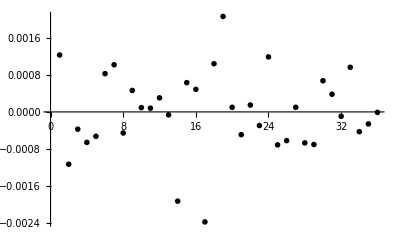

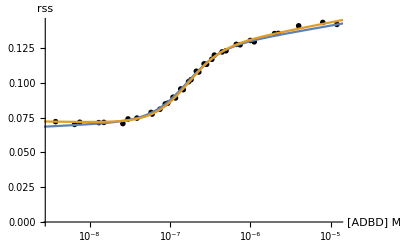

0.0000264091

```mathematica
nlmFull20TSGccAmicro["BestFitParameters"]
nlmFull20TSGccAmicro["ParameterErrors"]
ListPlot[nlmFull20TSGccAmicro["FitResiduals"],PlotTheme->"Monochrome"]
Show[ListLogLinearPlot[{Full2018Jan26A20,Full2018Feb15A20},PlotRange->All,AxesLabel->{"[ADBD] M","rss"}, PlotTheme->"Monochrome"],LogLinearPlot[{fullGRETSG20fitModelAmicro[gr,10^-8,kd,bb0,mb0,bu0,mu0,bb1,mb1,bu1,mu1,0]/.nlmFull20TSGccAmicro["BestFitParameters"],fullGRETSG20fitModelAmicro[gr,10^-8,kd,bb0,mb0,bu0,mu0,bb1,mb1,bu1,mu1,1]/.nlmFull20TSGccAmicro["BestFitParameters"]},{gr,10^-9,5*10^-5}]]
Total[nlmFull20TSGccAmicro["FitResiduals"]^2]
```

### NLM for C3:

```mathematica
nlmFull20TSGccC3micro=NonlinearModelFit[globalFull20TSGccC3,fullGRETSG20fitModelC3micro[gr,10^-8,kd,bb0,mb0,bu0,mu0,bb1,mb1,bu1,mu1,set],{{kd,1*10^-7},{bb0,0.17019234012406864},{mb0,0.0037715448028710586},{bu0,0.06827558418500337},{bb1,0.17019234012406864},{mb1,0.0037715448028710586},{bu1,0.06827558418500337},{mu0,0.001},{mu1,0.001}},{set,gr},MaxIterations->500]
```

FittedModel[Which[«1»]]

{kd→9.17196×10^-8,bb0→0.181247,mb0→0.00321006,bu0→0.11166,bb1→0.145259,mb1→0.000995058,bu1→0.0581642,mu0→0.00189212,mu1→-0.000997519}

{4.07355×10^-9,0.00569427,0.000413186,0.00994782,0.00494113,0.000363947,0.0112026,0.000540713,0.000606647}

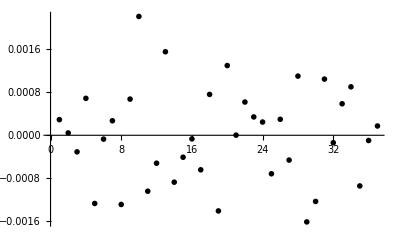

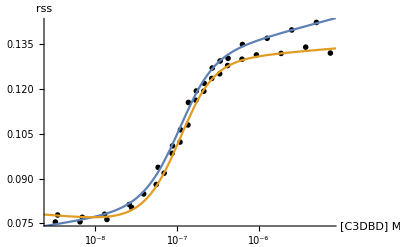

0.0000284995

```mathematica
nlmFull20TSGccC3micro["BestFitParameters"]
nlmFull20TSGccC3micro["ParameterErrors"]
ListPlot[nlmFull20TSGccC3micro["FitResiduals"],PlotTheme->"Monochrome"]
Show[ListLogLinearPlot[{Full2018Jan26C320,Full2018Feb15C320},PlotRange->All,AxesLabel->{"[C3DBD] M","rss"}, PlotTheme->"Monochrome"],LogLinearPlot[{fullGRETSG20fitModelC3micro[gr,10^-8,kd,bb0,mb0,bu0,mu0,bb1,mb1,bu1,mu1,0]/.nlmFull20TSGccC3micro["BestFitParameters"],fullGRETSG20fitModelC3micro[gr,10^-8,kd,bb0,mb0,bu0,mu0,bb1,mb1,bu1,mu1,1]/.nlmFull20TSGccC3micro["BestFitParameters"]},{gr,10^-9,5*10^-5}]]
Total[nlmFull20TSGccC3micro["FitResiduals"]^2]
```

## Fit Full-GRE data with 100 µM TSG:

April 2nd, May 8th (C3 only on May 8th)

### Set up the models:

*Use micro*

```mathematica
fullGRETSGfitModelA[gr_,GRE_,kd_,bb0_,mb0_,bu0_,mu0_,bb1_,mb1_,bu1_,mu1_,bb2_,mb2_,bu2_,mu2_,bb3_,mb3_,bu3_,mu3_,bb4_,mb4_,bu4_,mu4_,set_]:=Which[set==0,Evaluate@twoCoopMicro[gr,kd,bb0,mb0,bu0,mu0,GRE],
set==1,Evaluate@twoCoopMicro[gr,kd,bb1,mb1,bu1,mu1,GRE],
set==2,Evaluate@twoCoopMicro[gr,kd,bb2,mb2,bu2,mu2,GRE],
set==3,Evaluate@twoCoopMicro[gr,kd,bb3,mb3,bu3,mu3,GRE],
set==4,Evaluate@twoCoopMicro[gr,kd,bb4,mb4,bu4,mu4,GRE]];
```

```mathematica
fullGRETSGfitModelC3[gr_,GRE_,kd_,bb0_,mb0_,bu0_,mu0_,bb1_,mb1_,bu1_,mu1_,bb2_,mb2_,bu2_,mu2_,set_]:=Which[set==0,Evaluate@twoCoopMicro[gr,kd,bb0,mb0,bu0,mu0,GRE],
set==1,Evaluate@twoCoopMicro[gr,kd,bb1,mb1,bu1,mu1,GRE],
set==2,Evaluate@twoCoopMicro[gr,kd,bb2,mb2,bu2,mu2,GRE]];
```

### Label the datasets:

```mathematica
FullTSGccA=Join[FullTSGApril17A/.{x_,y_}->{0,x,y},
Full2017May26A100/.{x_,y_}->{1,x,y},
FullTSGJune17A/.{x_,y_}->{2,x,y},
Full2018Mar01A100/.{x_,y_}->{3,x,y},
Full2018Mar08A100/.{x_,y_}->{4,x,y}];
```

```mathematica
FullTSGccC3=Join[FullTSGccMay7C3/.{x_,y_}->{0,x,y},
Full2018Mar01C3100/.{x_,y_}->{1,x,y},
Full2018Mar08C3100/.{x_,y_}->{2,x,y}];
```

### NLM for A:

```mathematica
nlmFullTSGccA=NonlinearModelFit[FullTSGccA,fullGRETSGfitModelA[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,mu1,bb2,mb2,bu2,mu2,bb3,mb3,bu3,0,bb4,mb4,bu4,0,set],{{kd,5*10^-8},{bb0,0.17019234012406864},{mb0,0.0037715448028710586},{bu0,0.06827558418500337},{bb1,0.17019234012406864},{mb1,0.0037715448028710586},{bu1,0.06827558418500337},{bb2,0.17019234012406864},{mb2,0.0037715448028710586},{bu2,0.06827558418500337},{mu1,0.0},{mu2,0.0},{bb3,0.16},{mb3,0},{bu3,0.068},{bb4,0.16},{mb4,0.0},{bu4,0.068}},{set,gr},MaxIterations->500]
```

FittedModel[Which[set==0,«8»,0.0654671 (1-100000000 (1/3 (1/100000000+gr)+(«1»)/(24 «1»)-1/6 (-1/(«24»)+«6»+«1»)^(1/3)))+100000000 «1» («1»)]]

{kd→1.00341×10^-7,bb0→0.181599,mb0→0.00476833,bu0→0.0628844,bb1→0.194361,mb1→0.00475831,bu1→0.110219,bb2→0.206188,mb2→0.00685445,bu2→0.10145,mu1→0.00116485,mu2→0.00157856,bb3→0.195514,mb3→0.00543893,bu3→0.0666228,bb4→0.22094,mb4→0.00704292,bu4→0.0654671}

{4.03335×10^-9,0.00495646,0.000382676,0.000613179,0.00545581,0.000397845,0.00921912,0.00475033,0.0003634,0.0089053,0.000509817,0.000482007,0.00605379,0.00044365,0.00065595,0.00748253,0.000539797,0.00064965}

99

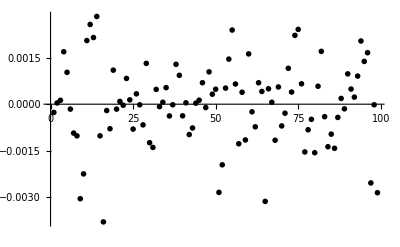

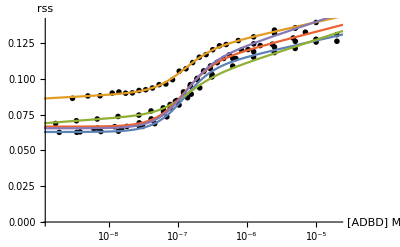

0.000166144

-8.0251×10^-9

```mathematica
nlmFullTSGccA["BestFitParameters"]
nlmFullTSGccA["ParameterErrors"]
Length[nlmFullTSGccA["Response"]]
ListPlot[nlmFullTSGccA["FitResiduals"],PlotTheme->"Monochrome"]
Show[ListLogLinearPlot[{FullTSGApril17A,Full2017May26A100,FullTSGJune17A,Full2018Mar01A100,Full2018Mar08A100},PlotRange->All,AxesLabel->{"[ADBD] M","rss"}, PlotTheme->"Monochrome"],LogLinearPlot[{fullGRETSGfitModelA[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,mu1,bb2,mb2,bu2,mu2,bb3,mb3,bu3,0,bb4,mb4,bu4,0,0]/.nlmFullTSGccA["BestFitParameters"],fullGRETSGfitModelA[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,mu1,bb2,mb2,bu2,mu2,bb3,mb3,bu3,0,bb4,mb4,bu4,0,1]/.nlmFullTSGccA["BestFitParameters"],
fullGRETSGfitModelA[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,mu1,bb2,mb2,bu2,mu2,bb3,mb3,bu3,0,bb4,mb4,bu4,0,2]/.nlmFullTSGccA["BestFitParameters"],
fullGRETSGfitModelA[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,mu1,bb2,mb2,bu2,mu2,bb3,mb3,bu3,0,bb4,mb4,bu4,0,3]/.nlmFullTSGccA["BestFitParameters"],fullGRETSGfitModelA[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,mu1,bb2,mb2,bu2,mu2,bb3,mb3,bu3,0,bb4,mb4,bu4,0,4]/.nlmFullTSGccA["BestFitParameters"]},{gr,10^-9,5*10^-5}]]
Total[nlmFullTSGccA["FitResiduals"]^2]
nlmFullTSGccA["ParameterErrors"][[1]]*y/.NMinimize[(0.975-CDF[StudentTDistribution[0
,1
,Length[nlmFullTSGccA["Response"]]-18],x][[2]]/.{x->y})^2
,y][[2]](*95% Conf interval for Kd*)
```

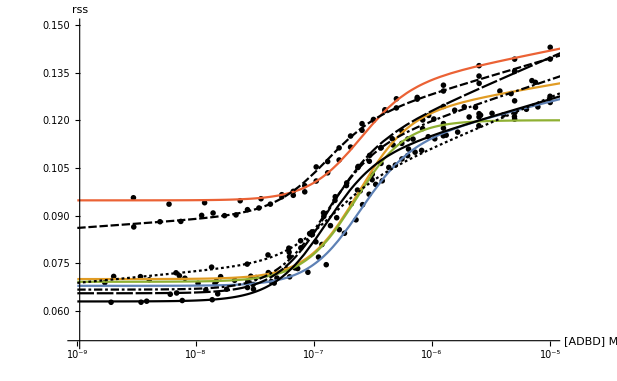

```mathematica
Show[ListLogLinearPlot[{FullMarch31A,FullMay27A,FullApril2A,FullApril17A,FullTSGApril17A,FullTSGJune17A,Full2018Mar01A100,Full2018Mar08A100,Full2017May26A100},PlotRange->{{10^-9,10^-5},{0.05,0.15}},AxesLabel->{"[ADBD] M","rss"}, PlotTheme->"Monochrome"],LogLinearPlot[{fullGREfitModelAmicro[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,0,bb2,0,bu2,0,bb3,mb3,bu3,0,0]/.nlmFullAmicro["BestFitParameters"],fullGREfitModelAmicro[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,0,bb2,0,bu2,0,bb3,mb3,bu3,0,1]/.nlmFullAmicro["BestFitParameters"],fullGREfitModelAmicro[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,0,bb2,0,bu2,0,bb3,mb3,bu3,0,2]/.nlmFullAmicro["BestFitParameters"],fullGREfitModelAmicro[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,0,bb2,0,bu2,0,bb3,mb3,bu3,0,3]/.nlmFullAmicro["BestFitParameters"]},{gr,10^-9,5*10^-5}],LogLinearPlot[{fullGRETSGfitModelA[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,mu1,bb2,mb2,bu2,mu2,bb3,mb3,bu3,0,bb4,mb4,bu4,0,0]/.nlmFullTSGccA["BestFitParameters"],fullGRETSGfitModelA[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,mu1,bb2,mb2,bu2,mu2,bb3,mb3,bu3,0,bb4,mb4,bu4,0,1]/.nlmFullTSGccA["BestFitParameters"],
fullGRETSGfitModelA[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,mu1,bb2,mb2,bu2,mu2,bb3,mb3,bu3,0,bb4,mb4,bu4,0,2]/.nlmFullTSGccA["BestFitParameters"],
fullGRETSGfitModelA[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,mu1,bb2,mb2,bu2,mu2,bb3,mb3,bu3,0,bb4,mb4,bu4,0,3]/.nlmFullTSGccA["BestFitParameters"],
fullGRETSGfitModelA[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,mu1,bb2,mb2,bu2,mu2,bb3,mb3,bu3,0,bb4,mb4,bu4,0,4]/.nlmFullTSGccA["BestFitParameters"]},{gr,10^-9,5*10^-5},PlotTheme->"Monochrome"]]
```

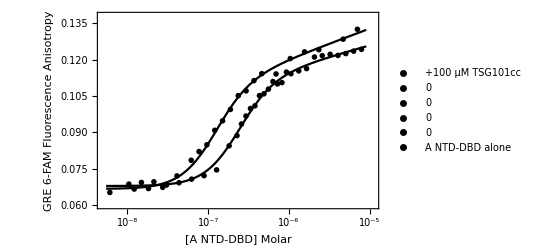

```mathematica
Show[ListLogLinearPlot[{Full2018Mar01A100,{1,1},{1,1},{1,1},{1,1},FullMarch31A},FrameLabel->{"[A NTD-DBD] Molar","GRE 6-FAM Fluorescence Anisotropy"}, PlotTheme->"Monochrome",Frame->True,PlotRange->{{5*10^-9,1.1*10^-5},{0.06,0.138}},PlotLegends->{"+100 µM TSG101cc","0","0","0","0","A NTD-DBD alone"}],LogLinearPlot[fullGREfitModelAmicro[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,0,bb2,0,bu2,0,bb3,mb3,bu3,0,0]/.nlmFullAmicro["BestFitParameters"],{gr,5.5*10^-9,9*10^-6},PlotTheme->"Monochrome"],
LogLinearPlot[fullGRETSGfitModelA[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,mu1,bb2,mb2,bu2,mu2,bb3,mb3,bu3,0,bb4,mb4,bu4,0,3]/.nlmFullTSGccA["BestFitParameters"],{gr,5.5*10^-9,9*10^-6},PlotTheme->"Monochrome"]]
```

#### dG Calculation for A+100 µM TSG101cc

```mathematica
R=1.987;
R*293.15*Log[(1.2079495568731876*^-7+6.934830269768482*^-9)/(2.0192053443538756*^-7-8.599372360190703*^-9)]
R*293.15*Log[1.2079495568731876*^-7/2.0192053443538756*^-7]
R*293.15*Log[(1.2079495568731876*^-7-6.934830269768482*^-9)/(2.0192053443538756*^-7+8.599372360190703*^-9)]
```

-241.404

-299.271

-358.003

Perhaps as much as ~0.3 kcal/mol of energy being gained.

### NLM for C3:

```mathematica
nlmFullTSGccC3=NonlinearModelFit[FullTSGccC3,fullGRETSGfitModelC3[gr,10^-8,kd,bb0,mb0,bu0,mu0,bb1,mb1,bu1,0,bb2,mb2,bu2,0,set],{{kd,1*10^-7},{bb0,0.17019234012406864},{mu0,0.001},{mb0,0.0037715448028710586},{bu0,0.06827558418500337},{bb1,0.17019234012406864},{mb1,0.0037715448028710586},{bu1,0.06827558418500337},(*{mu1,0.001},*){bb2,0.17019234012406864},{mb2,0.0037715448028710586},{bu2,0.06827558418500337}},{set,gr},MaxIterations->500]
```

FittedModel[Which[set==0,«4»,0.0786822 (1-100000000 (1/3 (1/100000000+gr)+(-1/(«14»0)+«3»+12 «1»)/(24 («1»)^(1/3))-1/6 («1»)^(1/3)))+100000000 «1» («1»)]]

{kd→9.45453×10^-8,bb0→0.24639,mu0→0.00196024,mb0→0.0101775,bu0→0.0958317,bb1→0.194167,mb1→0.0043946,bu1→0.0752672,bb2→0.212454,mb2→0.00564468,bu2→0.0786822}

{2.54215×10^-9,0.00263751,0.000225704,0.000198549,0.00422923,0.00370724,0.000273787,0.000413885,0.00449928,0.00032502,0.000392164}

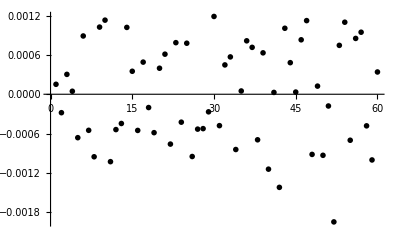

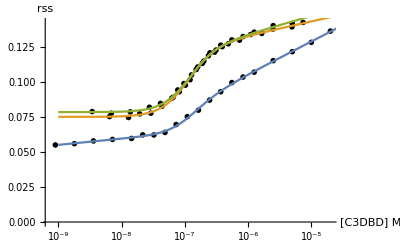

0.0000348127

-5.10865×10^-9

```mathematica
nlmFullTSGccC3["BestFitParameters"]
nlmFullTSGccC3["ParameterErrors"]
ListPlot[nlmFullTSGccC3["FitResiduals"],PlotTheme->"Monochrome"]
Show[ListLogLinearPlot[{FullTSGccMay7C3,Full2018Mar01C3100,Full2018Mar08C3100},PlotRange->All,AxesLabel->{"[C3DBD] M","rss"}, PlotTheme->"Monochrome"],LogLinearPlot[{fullGRETSGfitModelC3[gr,10^-8,kd,bb0,mb0,bu0,mu0,bb1,mb1,bu1,0,bb2,mb2,bu2,0,0]/.nlmFullTSGccC3["BestFitParameters"],fullGRETSGfitModelC3[gr,10^-8,kd,bb0,mb0,bu0,mu0,bb1,mb1,bu1,0,bb2,mb2,bu2,0,1]/.nlmFullTSGccC3["BestFitParameters"],fullGRETSGfitModelC3[gr,10^-8,kd,bb0,mb0,bu0,mu0,bb1,mb1,bu1,0,bb2,mb2,bu2,0,2]/.nlmFullTSGccC3["BestFitParameters"]},{gr,10^-9,5*10^-5}]]
Total[nlmFullTSGccC3["FitResiduals"]^2]
nlmFullTSGccC3["ParameterErrors"][[1]]*y/.NMinimize[(0.975-CDF[StudentTDistribution[0
,1
,Length[nlmFullTSGccC3["Response"]]-11],x][[2]]/.{x->y})^2
,y][[2]](*95% Conf interval for Kd*)
```

#### dG Calculation for C3+100 µM TSG101cc

```mathematica
R=1.987;
R*293.15*Log[(9.454525303745983*^-8+2.5421535588049677*^-9)/(2.2854895933130998*^-7-1.1832067567054142*^-8)]
R*293.15*Log[9.454525303745983*^-8/2.2854895933130998*^-7]
R*293.15*Log[(9.454525303745983*^-8-2.5421535588049677*^-9)/(2.2854895933130998*^-7+1.1832067567054142*^-8)]
```

-437.984

-491.595

-544.559

Perhaps as much as ~0.5 kcal/mol of energy being gained.

## Fit Full-GRE data with 200 µM TSG:

2018 Jan 26 and Feb 15

### Set up the models:

```mathematica
fullGRETSG200fitModelAmicro[gr_,GRE_,kd_,bb0_,mb0_,bu0_,mu0_,bb1_,mb1_,bu1_,mu1_,set_]:=Which[set==0,Evaluate@twoCoopMicro[gr,kd,bb0,mb0,bu0,mu0,GRE],
set==1,Evaluate@twoCoopMicro[gr,kd,bb1,mb1,bu1,mu1,GRE]];
fullGRETSG200fitModelC3micro[gr_,GRE_,kd_,bb0_,mb0_,bu0_,mu0_,bb1_,mb1_,bu1_,mu1_,set_]:=Which[set==0,Evaluate@twoCoopMicro[gr,kd,bb0,mb0,bu0,mu0,GRE],
set==1,Evaluate@twoCoopMicro[gr,kd,bb1,mb1,bu1,mu1,GRE]];
```

### Label the datasets:

```mathematica
globalFull200TSGccA=Join[Full2018Jan26A200/.{x_,y_}->{0,x,y},
Full2018Feb15A200/.{x_,y_}->{1,x,y}];
```

```mathematica
globalFull200TSGccC3=Join[Full2018Jan26C3200/.{x_,y_}->{0,x,y},
Full2018Feb15C3200/.{x_,y_}->{1,x,y}];
```

### NLM for A:

```mathematica
nlmFull200TSGccAmicro=NonlinearModelFit[globalFull200TSGccA,fullGRETSG200fitModelAmicro[gr,10^-8,kd,bb0,mb0,bu0,mu0,bb1,mb1,bu1,mu1,set],{{kd,1*10^-7},{bb0,0.17019234012406864},{mb0,0.0037715448028710586},{bu0,0.06827558418500337},{bb1,0.17019234012406864},{mb1,0.0037715448028710586},{bu1,0.06827558418500337},{mu0,0.001},{mu1,0.001}},{set,gr},MaxIterations->500]
```

FittedModel[Which[«1»]]

{kd→1.21259×10^-7,bb0→0.229095,mb0→0.00726823,bu0→0.0892163,bb1→0.238302,mb1→0.00813054,bu1→0.068725,mu0→0.0013864,mu1→0.000142915}

{7.2115×10^-9,0.010975,0.000796978,0.0112872,0.00535502,0.00041315,0.0120499,0.000630316,0.000673111}

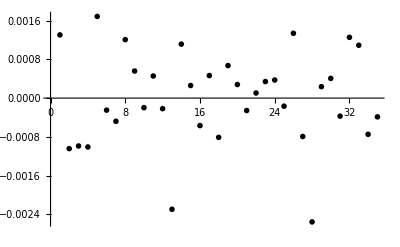

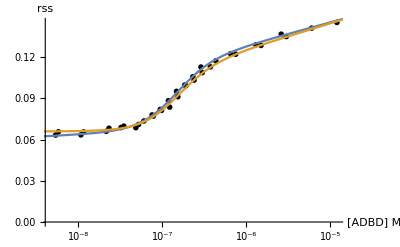

0.000031458

```mathematica
nlmFull200TSGccAmicro["BestFitParameters"]
nlmFull200TSGccAmicro["ParameterErrors"]
ListPlot[nlmFull200TSGccAmicro["FitResiduals"],PlotTheme->"Monochrome"]
Show[ListLogLinearPlot[{Full2018Jan26A200,Full2018Feb15A200},PlotRange->All,AxesLabel->{"[ADBD] M","rss"}, PlotTheme->"Monochrome"],LogLinearPlot[{fullGRETSG200fitModelAmicro[gr,10^-8,kd,bb0,mb0,bu0,mu0,bb1,mb1,bu1,mu1,0]/.nlmFull200TSGccAmicro["BestFitParameters"],fullGRETSG200fitModelAmicro[gr,10^-8,kd,bb0,mb0,bu0,mu0,bb1,mb1,bu1,mu1,1]/.nlmFull200TSGccAmicro["BestFitParameters"]},{gr,10^-9,5*10^-5}]]
Total[nlmFull200TSGccAmicro["FitResiduals"]^2]
```

### NLM for C3:

```mathematica
nlmFull200TSGccC3micro=NonlinearModelFit[globalFull200TSGccC3,fullGRETSG200fitModelC3micro[gr,10^-8,kd,bb0,mb0,bu0,mu0,bb1,mb1,bu1,mu1,set],{{kd,1*10^-7},{bb0,0.17019234012406864},{mb0,0.0037715448028710586},{bu0,0.06827558418500337},{bb1,0.17019234012406864},{mb1,0.0037715448028710586},{bu1,0.06827558418500337},{mu0,0.001},{mu1,0.001}},{set,gr},MaxIterations->500]
```

FittedModel[Which[«1»]]

{kd→1.00601×10^-7,bb0→0.194436,mb0→0.00535487,bu0→0.0962178,bb1→0.194327,mb1→0.00447223,bu1→0.0795255,mu0→0.00175686,mu1→0.000363907}

{3.76649×10^-9,0.00443347,0.000323398,0.00785627,0.00337538,0.000255489,0.00870869,0.000431906,0.000480061}

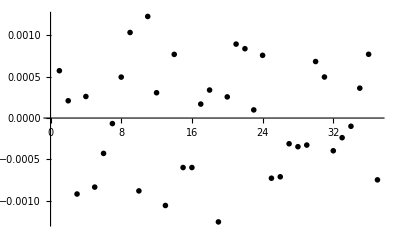

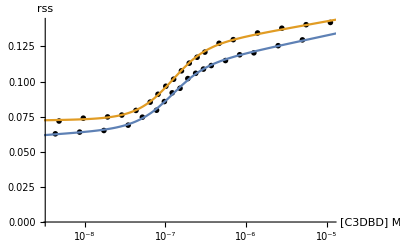

0.0000157618

```mathematica
nlmFull200TSGccC3micro["BestFitParameters"]
nlmFull200TSGccC3micro["ParameterErrors"]
ListPlot[nlmFull200TSGccC3micro["FitResiduals"],PlotTheme->"Monochrome"]
Show[ListLogLinearPlot[{Full2018Jan26C3200,Full2018Feb15C3200},PlotRange->All,AxesLabel->{"[C3DBD] M","rss"}, PlotTheme->"Monochrome"],LogLinearPlot[{fullGRETSG200fitModelC3micro[gr,10^-8,kd,bb0,mb0,bu0,mu0,bb1,mb1,bu1,mu1,0]/.nlmFull200TSGccC3micro["BestFitParameters"],fullGRETSG200fitModelC3micro[gr,10^-8,kd,bb0,mb0,bu0,mu0,bb1,mb1,bu1,mu1,1]/.nlmFull200TSGccC3micro["BestFitParameters"]},{gr,10^-9,5*10^-5}]]
Total[nlmFull200TSGccC3micro["FitResiduals"]^2]
```

### Consider the ddG versus TSG concentration for A and C3 GR

Take Kd’s from the individual, not global fits, except for the w/out TSG101cc reference (use global fit). That will build a better statistical rigor.

```mathematica
R=1.987; (*cal/K/mol*)
T=293.15;(*K*)
```

```mathematica
dG[kd_]:=-R*T*Log[kd];
```

TSG101cc binding NTD:

```mathematica
dG[2.0*10^-5]
```

6302.4

TSG101cc binding A--DBD in absence of GRE:

```mathematica
dG[3.4*10^-5]
```

5993.32

TSG101cc binding C3--DBD in absence of GRE:

```mathematica
dG[7.3*10^-5]
```

5548.24

A and C3 binding GRE without TSG101cc:

```mathematica
dG[2.1229464080281134*^-7](*A*)
dG[2.2854895933130998*^-7](*C3*)
```

8950.11

A and C3 binding GRE with TSG101cc:

```mathematica
dG[1.0478387561426536*^-7](*A*)
dG[9.486725135588888*^-8](*C3*)
```

9361.39

9419.31

Global fitted ddG’s:

```mathematica
dG[2.1229464080281134*^-7]-dG[1.0478387561426536*^-7](*A*)
dG[2.2854895933130998*^-7]-dG[9.486725135588888*^-8](*C3*)
```

-411.281

-512.166

Without log unbound baselines except where absolutely necessary:
ADBD+100µM TSG on May 26 and June 17, 2017 requires Log unbound
C3DBD “ from May 7, 2017

```mathematica
ddGA=dG[2.1229464080281134*^-7]-dG[{1.722989521916734*^-7,2.3070962081194956*^-7,2.234648927970857*^-7,1.7228909736926356*^-7,2.2966635793127584*^-7,1.5178933453058287*^-7,1.3472585855879997*^-7,1.3841469925907165*^-7,1.6698254465754513*^-7,1.2837311163855102*^-7,1.4996207546179433*^-7,1.1810841646626958*^-7,1.3541902774879853*^-7,1.1117130209769008*^-7,1.69575700319022*^-7,8.320845985882707*^-8,8.107418179060526*^-8,1.268644268894451*^-7,1.0087946208181831*^-7}];(*0.2, 0.4, 0.7, 2, 2, 7, 7, 20, 20, 100, 100, 100, 100, 100, 200, 200 µM and take from w/out TSG Kd*)
ddGC3=dG[2.2854895933130998*^-7]-dG[{2.254647773819279*^-7,1.7080865552231183*^-7,1.8348026631760605*^-7,2.218543321508031*^-7,1.719428637376686*^-7,2.27646173468851*^-7,1.7661192835664854*^-7,1.4833166615448114*^-7,1.0758649994913126*^-7,1.5385857277797058*^-7,1.0058933793783396*^-7,7.692509452815618*^-8,9.335528015664775*^-8,9.134209305568858*^-8,1.001822387790065*^-7,1.0102873602404877*^-7,8.344170346918743*^-8}];(*0.2, 0.4, 0.7, 2, 2, 20, 20, 100, 100, 100, 100, 200, 200 µM and take from w/out TSG Kd*)
concentrationA={0.2,0.2,0.4, 0.4,0.7, 0.7, 2.,2.,7.0,7.0, 20., 20., 100.,  100., 100., 100.,100., 200., 200.}*10^-6;
concentrationC3={0.2,0.2,0.4, 0.4,0.7, 0.7, 2.,2.,7.0,7., 20., 20., 100., 100., 100., 200., 200.}*10^-6;
plotA=Transpose[{concentrationA,ddGA}]
plotC3=Transpose[{concentrationC3,ddGC3}]
```

{{2.×10^-7,-121.591},{2.×10^-7,48.4542},{4.×10^-7,29.8696},{4.×10^-7,-121.624},{7.×10^-7,45.8142},{7.×10^-7,-195.414},{2.×10^-6,-264.877},{2.×10^-6,-249.143},{7.×10^-6,-139.847},{7.×10^-6,-293.012},{0.00002,-202.469},{0.00002,-341.555},{0.0001,-261.888},{0.0001,-376.814},{0.0001,-130.871},{0.0001,-545.574},{0.0001,-560.71},{0.0002,-299.898},{0.0002,-433.4}}

{{2.×10^-7,-7.91399},{2.×10^-7,-169.625},{4.×10^-7,-127.94},{4.×10^-7,-17.3171},{7.×10^-7,-165.77},{7.×10^-7,-2.30543},{2.×10^-6,-150.163},{2.×10^-6,-251.81},{7.×10^-6,-438.879},{7.×10^-6,-230.501},{0.00002,-478.051},{0.00002,-634.283},{0.0001,-521.525},{0.0001,-534.223},{0.0001,-480.413},{0.0002,-475.512},{0.0002,-586.917}}

```mathematica
SetDirectory["/Users/jordanwhite/Documents/My_Research/Hilser_Lab/Steady State Anisotropy/"]
```

/Users/jordanwhite/Documents/My_Research/Hilser_Lab/Steady State Anisotropy

```mathematica
Export["ADBD+GRE+TSG101ccTitration.csv",plotA];
Export["C3DBD+GRE+TSG101ccTitration.csv",plotC3];
```

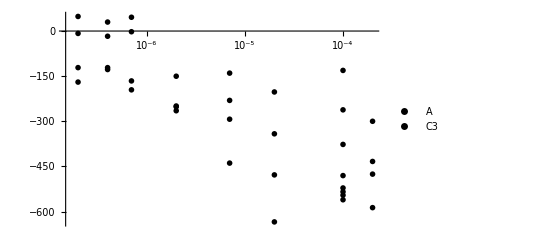

```mathematica
ListLogLinearPlot[{plotA,plotC3},PlotTheme->"Monochrome",PlotLegends->{"A","C3"}]
```

Try fitting the data using the single binding site polynomial

(dG_(GR-DNA))^App=-RT*ln(Kd w/out TSG) +dG_(GR-TSG)*Frac_GR_Bound
where the first part has already been subtracted in my data (I have delta-delta G’s plotted above), dG of GR-TSG is going to be the baseline for the bound state, and the fraction of GR bound by TSG will be described by the Kd...unclear what the best equation (partition or polynomial) is for this. Let’s assume the partition function b/c I don’t know what GR concentrations to be using here. Maybe a massive global fit using two independent variables ([GR] and [TSG]) would get at this better.

```mathematica
fracGRBound[tsg_,kd_]:=(tsg/kd)/(1+tsg/kd);
```

```mathematica
ddGapparent[dGbase_,tsg_,kd_]:=dGbase*fracGRBound[tsg,kd];(*unbound base is zero, so excluded here*)
```

What about two independent sites?

```mathematica
fracGRxGREboundIndependent[tsg_,kd_]:=(2*tsg/kd+2*(tsg/kd)^2)/(1+2*tsg/kd+(tsg/kd)^2);
```

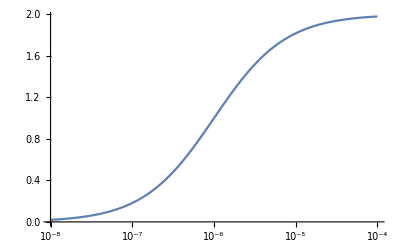

```mathematica
LogLinearPlot[fracGRxGREboundIndependent[tsg,10^-6],{tsg,10^-8,10^-4}]
```

```mathematica
ddGapparentIndependent[dGbase_,tsg_,kd_]:=dGbase*fracGRxGREboundIndependent[tsg,kd];
```

#### A isoform

```mathematica
nlmAddG=NonlinearModelFit[plotA,ddGapparent[dGbase,tsg,kd],{{dGbase,-400},{kd,2*10^-6}},tsg]
```

FittedModel[-(1.79552×10^8 tsg)/(1+499631. tsg)]

{dGbase→-359.369,kd→2.00148×10^-6}

{44.0834,1.38148×10^-6}

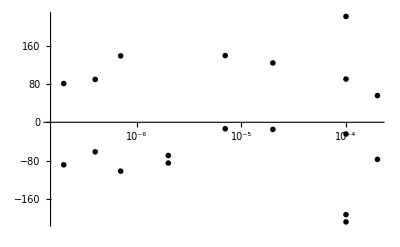

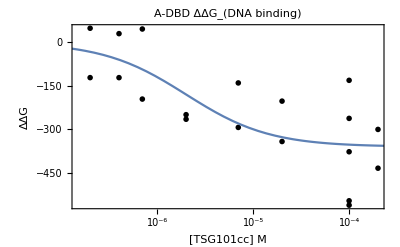

251288.

-93.0078

-2.91466×10^-6

```mathematica
nlmAddG["BestFitParameters"]
nlmAddG["ParameterErrors"]
ListLogLinearPlot[Transpose[{concentrationA,nlmAddG["FitResiduals"]}],PlotTheme->"Monochrome"]
Show[ListLogLinearPlot[plotA,PlotRange->All,PlotLabel->"A-DBD ΔΔG_(DNA binding)",FrameLabel->{"[TSG101cc] M","ΔΔG"}, Frame->True,PlotTheme->"Monochrome"],LogLinearPlot[ddGapparent[dGbase,tsg,kd]/.nlmAddG["BestFitParameters"],{tsg,10^-8,2.5*10^-4}]]
Total[nlmAddG["FitResiduals"]^2]
nlmAddG["ParameterErrors"][[1]]*y/.NMinimize[(0.975-CDF[StudentTDistribution[0
,1
,Length[nlmAddG["Response"]]-Length[nlmAddG["ParameterErrors"]]],x][[2]]/.{x->y})^2
,y][[2]](*95% Conf interval for ddG*)
nlmAddG["ParameterErrors"][[2]]*y/.NMinimize[(0.975-CDF[StudentTDistribution[0
,1
,Length[nlmAddG["Response"]]-Length[nlmAddG["ParameterErrors"]]],x][[2]]/.{x->y})^2
,y][[2]](*95% Conf interval for Kd*)
```

```mathematica
-R*T*Log[2.0014761840509556*^-6+nlmAddG["ParameterErrors"][[2]]*y/.NMinimize[(0.975-CDF[StudentTDistribution[0
,1
,Length[nlmAddG["Response"]]-Length[nlmAddG["ParameterErrors"]]],x][[2]]/.{x->y})^2
,y][[2]]](*95% Conf interval for Kd*)
```

8100.28-1829.94 ⅈ

```mathematica
Exp[-(7119.76)/(R*T)](*Upper bound in uM*)
Exp[-(8100.28)/(R*T)](*Lower bound in uM*)
```

4.91611×10^-6

9.1319×10^-7

The A isoform CI is confusing when in uM. Convert to kcal/mol to get something more meaningful.

```mathematica
-R*T*Log[(2.914660433187209*^-6+2.0014761840509556*^-6)/(2.0014761840509556*^-6)](*95% CI in cal/mol*)
-R*T*Log[(2.0014761840509556*^-6)](*dG centroid*)
```

-523.447

7643.2

```mathematica
Exp[-(7643.2-523.447)/(R*T)](*Upper bound in uM*)
Exp[-(7643.2+523.447)/(R*T)](*Lower bound in uM*)
```

4.91617×10^-6

8.14853×10^-7

```mathematica
Export["/Users/jordanwhite/Documents/My_Research/Hilser_Lab/Steady State Anisotropy/20180311_ADBD_ddG-DNA+TSG101cc.pdf",%497,"PDF"]
```

/Users/jordanwhite/Documents/My_Research/Hilser_Lab/Steady State Anisotropy/20180311_ADBD_ddG-DNA+TSG101cc.pdf

Now try with 2 independent sites

```mathematica
nlmAddGindependent=NonlinearModelFit[plotA,ddGapparentIndependent[dGbase,tsg,kd],{{dGbase,-400},{kd,2*10^-6}},tsg]
```

```mathematica
nlmAddGindependent["BestFitParameters"]
nlmAddGindependent["ParameterErrors"]
ListLogLinearPlot[Transpose[{concentrationA,nlmAddGindependent["FitResiduals"]}],PlotTheme->"Monochrome"]
Show[ListLogLinearPlot[plotA,PlotRange->All,PlotLabel->"A-DBD ΔΔG_(DNA binding)",FrameLabel->{"[TSG101cc] M","ΔΔG"}, Frame->True,PlotTheme->"Monochrome"],LogLinearPlot[ddGapparentIndependent[dGbase,tsg,kd]/.nlmAddGindependent["BestFitParameters"],{tsg,10^-8,2.5*10^-4}]]
Total[nlmAddGindependent["FitResiduals"]^2]
nlmAddGindependent["ParameterErrors"][[1]]*y/.NMinimize[(0.975-CDF[StudentTDistribution[0
,1
,Length[nlmAddGindependent["Response"]]-Length[nlmAddGindependent["ParameterErrors"]]],x][[2]]/.{x->y})^2
,y][[2]](*95% Conf interval for ddG*)
nlmAddGindependent["ParameterErrors"][[2]]*y/.NMinimize[(0.975-CDF[StudentTDistribution[0
,1
,Length[nlmAddGindependent["Response"]]-Length[nlmAddGindependent["ParameterErrors"]]],x][[2]]/.{x->y})^2
,y][[2]](*95% Conf interval for Kd*)
```

{dGbase→-179.684,kd→2.00148×10^-6}

{22.0417,1.38148×10^-6}

-Graphics-

-Graphics-

251288.

-46.5039

-2.91466×10^-6

#### C3 isoform

```mathematica
nlmC3ddG=NonlinearModelFit[plotC3,ddGapparent[dGbase,tsg,kd],{{dGbase,-500},{kd,2*10^-6}},tsg]
```

FittedModel[-(1.69582×10^8 tsg)/(1+307960. tsg)]

{dGbase→-550.661,kd→3.24717×10^-6}

{37.4728,1.09974×10^-6}

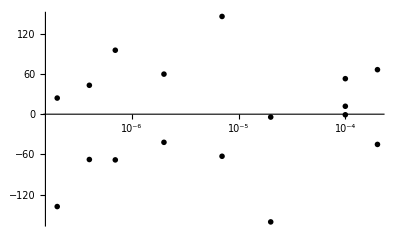

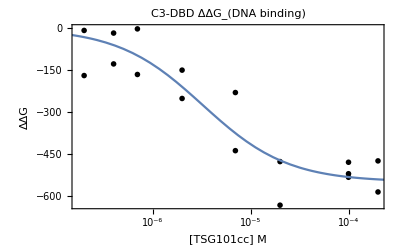

105323.

79.8715

2.34405×10^-6

```mathematica
nlmC3ddG["BestFitParameters"]
nlmC3ddG["ParameterErrors"]
ListLogLinearPlot[Transpose[{concentrationC3,nlmC3ddG["FitResiduals"]}],PlotTheme->"Monochrome"]
Show[ListLogLinearPlot[plotC3,PlotRange->All,PlotLabel->"C3-DBD ΔΔG_(DNA binding)",FrameLabel->{"[TSG101cc] M","ΔΔG"}, PlotTheme->"Monochrome",Frame->True],LogLinearPlot[ddGapparent[dGbase,tsg,kd]/.nlmC3ddG["BestFitParameters"],{tsg,10^-8,2.5*10^-4}]]
Total[nlmC3ddG["FitResiduals"]^2]
nlmC3ddG["ParameterErrors"][[1]]*y/.NMinimize[(0.975-CDF[StudentTDistribution[0
,1
,Length[nlmC3ddG["Response"]]-Length[nlmC3ddG["ParameterErrors"]]],x]/.{x->y})^2
,y][[2]](*95% Conf interval for ddG*)
nlmC3ddG["ParameterErrors"][[2]]*y/.NMinimize[(0.975-CDF[StudentTDistribution[0
,1
,Length[nlmC3ddG["Response"]]-Length[nlmC3ddG["ParameterErrors"]]],x]/.{x->y})^2
,y][[2]](*95% Conf interval for Kd*)
```

The C3 isoform CI is confusing when in uM. Convert to kcal/mol to get something more meaningful.

```mathematica
-R*T*Log[(2.34404943432087*^-6+3.2471724302939574*^-6)/(3.2471724302939574*^-6)](*95% CI in cal/mol*)
-R*T*Log[(3.2471724302939574*^-6)](*dG centroid*)
```

-316.532

7361.34

```mathematica
Exp[-(7361.34-316.532)/(R*T)](*Upper bound in uM*)
Exp[-(7361.34+316.532)/(R*T)](*Lower bound in uM*)
```

5.59119×10^-6

1.88583×10^-6

```mathematica
Export["/Users/jordanwhite/Documents/My_Research/Hilser_Lab/Steady State Anisotropy/20180311_C3DBD_ddG-DNA+TSG101cc.pdf",%491,"PDF"]
```

/Users/jordanwhite/Documents/My_Research/Hilser_Lab/Steady State Anisotropy/20180311_C3DBD_ddG-DNA+TSG101cc.pdf

### With log unbound baselines:

```mathematica
ddGA=dG[2.1229464080281134*^-7]-dG[{1.8371786228572524*^-7,2.3135904745433636*^-7,2.0669068383020221*^-7,1.5718075472822725*^-7,1.4256803722913386*^-7,2.0761942585577433*^-7,1.2692961811832828*^-7,1.43991163606845*^-7,1.548167840266608*^-7,1.5112012443065735*^-7,1.2059957002662387*^-7,9.475178025292913*^-8,9.07821793809868*^-8,1.1117130209769008*^-7,1.5892467270992005*^-7,1.69575700319022*^-7,1.0585711795659746*^-7,1.341157593490096*^-7}];(*0.2, 0.4, 0.7, 2, 2, 20, 20, 100, 100, 100, 100, 100, 200, 200 µM and take from w/out TSG Kd*)
ddGC3=dG[2.2854895933130998*^-7]-dG[{1.905276722769532*^-7,1.5624479770891545*^-7,1.7206723340329732*^-7,1.915841037327224*^-7,1.9652130795995646*^-7,1.4817007280889503*^-7,1.5617422752590217*^-7,1.4531137069121887*^-7,1.1044816568549356*^-7,9.754994416741791*^-8,8.478189143324757*^-8,1.0796223906185916*^-7,9.225486068691801*^-8,9.335528015664775*^-8,9.092684804849193*^-8,1.0745037794246004*^-7}];(*0.2, 0.4, 0.7, 2, 2, 20, 20, 100, 100, 100, 100, 200, 200 µM and take from w/out TSG Kd*)
concentrationA={0.2,0.2,0.4, 0.4,0.7, 0.7, 2.,2.,7.0, 20., 20., 100.,  100., 100., 100.,100., 200., 200.}*10^-6;
concentrationC3={0.2,0.2,0.4, 0.4,0.7, 0.7, 2.,2.,7.0, 20., 20., 100., 100., 100., 200., 200.}*10^-6;
plotAlog=Transpose[{concentrationA,ddGA}]
plotC3log=Transpose[{concentrationC3,ddGC3}]
```

#### A isoform

```mathematica
nlmAddGlog=NonlinearModelFit[plotAlog,ddGapparent[dGbase,tsg,kd],{{dGbase,-400},{kd,2*10^-6}},tsg]
```

FittedModel[-(3.65551×10^8 tsg)/(1+1.09986×10^6 tsg)]

{dGbase→-332.36,kd→9.09204×10^-7}

{37.9399,5.74925×10^-7}

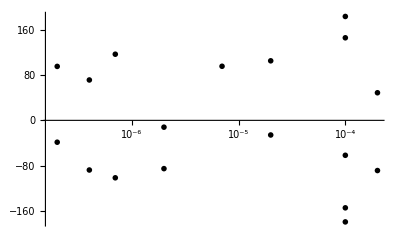

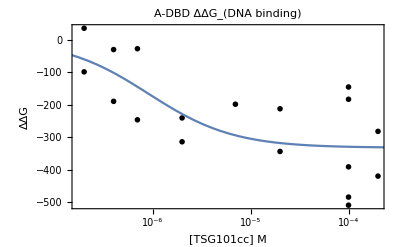

201804.

```mathematica
nlmAddGlog["BestFitParameters"]
nlmAddGlog["ParameterErrors"]
ListLogLinearPlot[Transpose[{concentrationA,nlmAddGlog["FitResiduals"]}],PlotTheme->"Monochrome"]
Show[ListLogLinearPlot[plotAlog,PlotRange->All,PlotLabel->"A-DBD ΔΔG_(DNA binding)",FrameLabel->{"[TSG101cc] M","ΔΔG"}, Frame->True,PlotTheme->"Monochrome"],LogLinearPlot[ddGapparent[dGbase,tsg,kd]/.nlmAddGlog["BestFitParameters"],{tsg,10^-8,2.5*10^-4}]]
Total[nlmAddGlog["FitResiduals"]^2]
```

```mathematica
Export["/Users/jordanwhite/Documents/My_Research/Hilser_Lab/Steady State Anisotropy/20180311_ADBD_ddG-DNA+TSG101cc.pdf",%497,"PDF"]
```

/Users/jordanwhite/Documents/My_Research/Hilser_Lab/Steady State Anisotropy/20180311_ADBD_ddG-DNA+TSG101cc.pdf

#### C3 isoform

```mathematica
nlmC3ddGlog=NonlinearModelFit[plotC3log,ddGapparent[dGbase,tsg,kd],{{dGbase,-500},{kd,2*10^-6}},tsg]
```

FittedModel[-(3.21645×10^8 tsg)/(1+652000. tsg)]

{dGbase→-493.321,kd→1.53374×10^-6}

{27.6767,4.3684×10^-7}

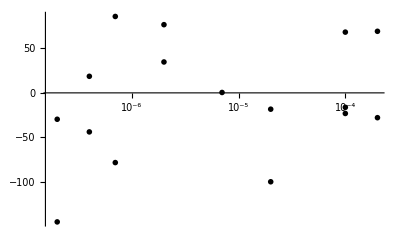

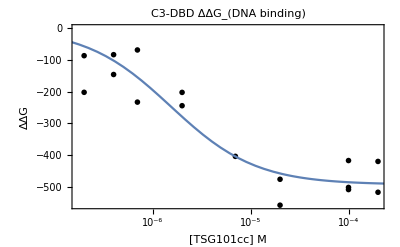

66343.1

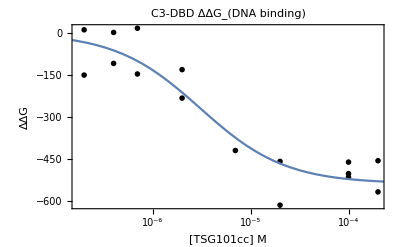

```mathematica
nlmC3ddGlog["BestFitParameters"]
nlmC3ddGlog["ParameterErrors"]
ListLogLinearPlot[Transpose[{concentrationC3,nlmC3ddGlog["FitResiduals"]}],PlotTheme->"Monochrome"]
Show[ListLogLinearPlot[plotC3log,PlotRange->All,PlotLabel->"C3-DBD ΔΔG_(DNA binding)",FrameLabel->{"[TSG101cc] M","ΔΔG"}, PlotTheme->"Monochrome",Frame->True],LogLinearPlot[ddGapparent[dGbase,tsg,kd]/.nlmC3ddGlog["BestFitParameters"],{tsg,10^-8,2.5*10^-4}]]
Total[nlmC3ddGlog["FitResiduals"]^2]
```

```mathematica
Export["/Users/jordanwhite/Documents/My_Research/Hilser_Lab/Steady State Anisotropy/20180311_C3DBD_ddG-DNA+TSG101cc.pdf",%491,"PDF"]
```

/Users/jordanwhite/Documents/My_Research/Hilser_Lab/Steady State Anisotropy/20180311_C3DBD_ddG-DNA+TSG101cc.pdf

If the binding of TSG to GR moved tenfold from 20 to 2 µM, that is equivalent to a ddG of:

```mathematica
dG[2.0*^-5]-dG[2.0*^-6]
```

-1341.23

```mathematica
-R*T*Log[20./2.]
```

-1341.23

How much energy is in the GR binding interactions with GRE and TSG101?

```mathematica
dG[2.0192053443538756*^-7]+dG[2.0*^-5]
```

15281.7

Given the change in DNA binding, how much energy is unaccounted for in the +TSG101cc circumstance?

```mathematica
dG[1.0*^-7]-(dG[2.0192053443538756*^-7]+dG[2.0*^-5])
```

-5893.08

What are the TSG101cc binding energies with DNA present?

```mathematica
dG[2.0*10^-6](*A*)
dG[3.2*10^-6](*C3*)
```

7643.63

7369.86

Difference between NTD DBD binding TSG101cc w/out versus with DNA also bound:

```mathematica
dG[2.0*10^-6]-dG[3.4*10^-5](*A*)
dG[3.2*10^-6]-dG[7.3*10^-5](*C3*)
```

1650.32

1821.62

## Fit Half-site w/out TSG data:

```mathematica
halfGREfitModelA[gr_,GRE_,kd_,bb0_,mb0_,bu0_,mu0_,bb1_,mb1_,bu1_,mu1_,bb2_,mb2_,bu2_,mu2_,set_]:=Which[set==0,Evaluate@signal[gr,GRE,kd,bb0,mb0,bu0,mu0],
set==1,Evaluate@signal[gr,GRE,kd,bb1,mb1,bu1,mu1],
set==2,Evaluate@signal[gr,GRE,kd,bb2,mb2,bu2,mu2]];
```

```mathematica
halfGREfitModelC3[gr_,GRE_,kd_,bb0_,mb0_,bu0_,mu0_,bb1_,mb1_,bu1_,mu1_,bb2_,mb2_,bu2_,mu2_,bb3_,mb3_,bu3_,mu3_,set_]:=Which[set==0,Evaluate@signal[gr,GRE,kd,bb0,mb0,bu0,mu0],
set==1,Evaluate@signal[gr,GRE,kd,bb1,mb1,bu1,mu1],
set==2,Evaluate@signal[gr,GRE,kd,bb2,mb2,bu2,mu2],
set==3,Evaluate@signal[gr,GRE,kd,bb3,mb3,bu3,mu3]];
```

```mathematica
(*halfGREfitModelC3[gr_,GRE_,kd_,bb0_,mb0_,bu0_,mu0_,bb1_,mb1_,bu1_,mu1_,set_]:=Which[set==0,Evaluate@signal[gr,GRE,kd,bb0,mb0,bu0,mu0],
set==1,Evaluate@signal[gr,GRE,kd,bb1,mb1,bu1,mu1]];*)
```

### Label the datasets:

```mathematica
globalHalfA=Join[HalfApril1A/.{x_,y_}->{0,x,y},
HalfApril3A/.{x_,y_}->{1,x,y},
HalfJune17A/.{x_,y_}->{2,x,y}];
globalHalfC3=Join[HalfApril1C3/.{x_,y_}->{0,x,y},
HalfApril3C3/.{x_,y_}->{1,x,y},
HalfMay8C3/.{x_,y_}->{2,x,y},
HalfMay26C3/.{x_,y_}->{3,x,y}];
(*globalHalfC3=Join[HalfApril1C3/.{x_,y_}->{0,x,y},
HalfApril3C3/.{x_,y_}->{1,x,y}];*)
```

### NLM for A:

```mathematica
nlmHalfA=NonlinearModelFit[globalHalfA,halfGREfitModelA[gr,10^-8,kd,bb0,0,bu0,0,bb1,0,bu1,0,bb2,0,bu2,0,set],{{kd,0.9*10^-6},{bb0,0.17019234012406864},{bu0,0.06827558418500337},{bb1,0.17019234012406864},{bu1,0.06827558418500337},{bb2,0.17019234012406864},{bu2,0.06827558418500337}(*,{mb0,0.0037715448028710586},{mb1,0.0037715448028710586},{mb2,0.0037715448028710586},{mu0,0.001},{mu1,0.001},{mu2,0.001}*)},{set,gr},MaxIterations->500]
```

FittedModel[Which[set==0,«4»,50000000 0.126537 (1/100000000+gr+1.33136×10^-6-√(-gr/25000000+(1/100000000+gr+«23»)^2))+«20» («1»)]]

{kd→1.33136×10^-6,bb0→0.11838,bu0→0.0681266,bb1→0.122972,bu1→0.0637614,bb2→0.126537,bu2→0.066822}

{1.17594×10^-7,0.00108124,0.00102298,0.00158807,0.00127003,0.00186997,0.00128053}

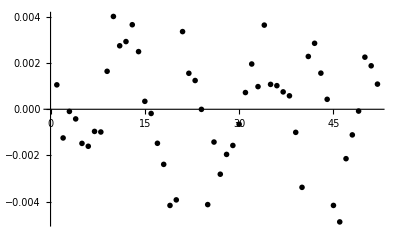

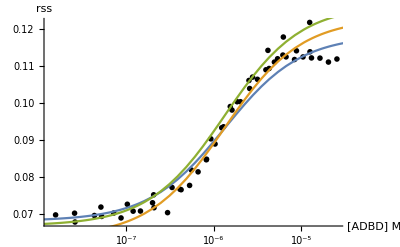

0.000260958

-2.36846×10^-7

```mathematica
nlmHalfA["BestFitParameters"]
nlmHalfA["ParameterErrors"]
ListPlot[nlmHalfA["FitResiduals"],PlotTheme->"Monochrome"]
Show[ListLogLinearPlot[{HalfApril1A,HalfApril3A,HalfJune17A},PlotRange->All,AxesLabel->{"[ADBD] M","rss"}, PlotTheme->"Monochrome"],LogLinearPlot[{halfGREfitModelA[gr,10^-8,kd,bb0,0,bu0,0,bb1,0,bu1,0,0,0,0,0,0]/.nlmHalfA["BestFitParameters"],halfGREfitModelA[gr,10^-8,kd,bb0,0,bu0,0,bb1,0,bu1,0,0,0,0,0,1]/.nlmHalfA["BestFitParameters"],
halfGREfitModelA[gr,10^-8,kd,bb0,0,bu0,0,bb1,0,bu1,0,bb2,0,bu2,0,2]/.nlmHalfA["BestFitParameters"]},{gr,10^-9,5*10^-5}]]
Total[nlmHalfA["FitResiduals"]^2]
nlmHalfA["ParameterErrors"][[1]]*y/.NMinimize[(0.975-CDF[StudentTDistribution[0
,1
,Length[nlmHalfA["Response"]]-7],x][[2]]/.{x->y})^2
,y][[2]](*95% Conf interval for Kd*)
```

Use of only constant baselines yields a fitted Kd ~1.3 µM and underfitting of the data. Log baselines seem to over fit the data slightly and Kd ~1.7 µM. Not clear which is best to use here. Shitty either way.

### NLM for C3:

```mathematica
nlmHalfC3=NonlinearModelFit[globalHalfC3,halfGREfitModelC3[gr,10^-8,kd,bb0,mb0,bu0,mu0,bb1,0,bu1,0,bb2,mb2,bu2,mu2,bb3,0,bu3,0,set],{{kd,1*10^-6},{bb0,0.12},{bu0,0.06827558418500337},{bb1,0.12},{bu1,0.06827558418500337},{bb2,0.12},{bu2,0.06827558418500337},{bb3,0.12},{bu3,0.07},{mb2,0.003},{mu2,0.003},{mb0,-0.001},{mu0,0.001}},{set,gr},MaxIterations->500]
```

FittedModel[Which[set==0,«6»,50000000 0.139439 (1/100000000+gr+1.5761×10^-6-√(-gr/25000000+(1/100000000+gr+«23»)^2))+«19» («1»)]]

{kd→1.5761×10^-6,bb0→0.0530094,bu0→0.00167998,bb1→0.129708,bu1→0.0650628,bb2→0.179219,bu2→0.0352783,bb3→0.139439,bu3→0.0705396,mb2→0.0043716,mu2→-0.00235301,mb0→-0.00695898,mu0→-0.00386408}

{6.76067×10^-8,0.0113888,0.0152355,0.000697472,0.000739446,0.0114749,0.00974114,0.000833188,0.000553465,0.00105559,0.00056972,0.00107798,0.000920495}

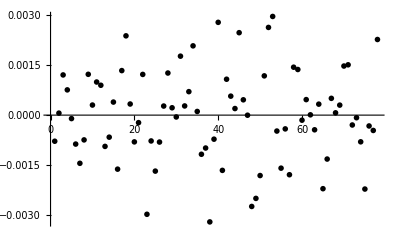

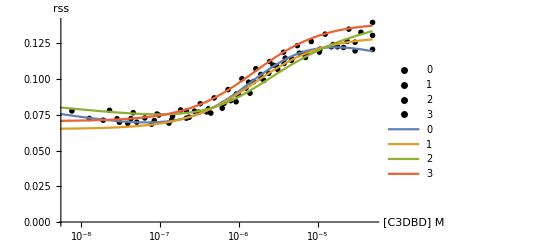

0.000144093

-1.3502×10^-7

```mathematica
nlmHalfC3["BestFitParameters"]
nlmHalfC3["ParameterErrors"]
ListPlot[nlmHalfC3["FitResiduals"],PlotTheme->"Monochrome"]
Show[ListLogLinearPlot[{HalfApril1C3,HalfApril3C3,HalfMay8C3,HalfMay26C3},PlotRange->All,AxesLabel->{"[C3DBD] M","rss"}, PlotTheme->"Monochrome",PlotLegends->{"0","1","2","3"}],LogLinearPlot[{halfGREfitModelC3[gr,10^-8,kd,bb0,mb0,bu0,mu0,bb1,0,bu1,0,bb2,0,bu2,0,bb3,0,bu3,0,0]/.nlmHalfC3["BestFitParameters"],halfGREfitModelC3[gr,10^-8,kd,bb0,0,bu0,0,bb1,0,bu1,0,bb2,0,bu2,0,bb3,0,bu3,0,1]/.nlmHalfC3["BestFitParameters"],halfGREfitModelC3[gr,10^-8,kd,bb0,0,bu0,0,bb1,0,bu1,0,bb2,mb2,bu2,mu2,bb3,0,bu3,0,2]/.nlmHalfC3["BestFitParameters"],
halfGREfitModelC3[gr,10^-8,kd,bb0,0,bu0,0,bb1,0,bu1,0,bb2,0,bu2,0,bb3,0,bu3,0,3]/.nlmHalfC3["BestFitParameters"]},{gr,10^-9,5*10^-5},PlotLegends->{"0","1","2","3"}]]
Total[nlmHalfC3["FitResiduals"]^2]
nlmHalfC3["ParameterErrors"][[1]]*y/.NMinimize[(0.975-CDF[StudentTDistribution[0
,1
,Length[nlmHalfC3["Response"]]-13],x][[2]]/.{x->y})^2
,y][[2]](*95% Conf interval for Kd*)
```

## Fit half-GRE + TSG101

```mathematica
halfGREfitModelAtsg[gr_,GRE_,kd_,bb0_,mb0_,bu0_,mu0_,bb1_,mb1_,bu1_,mu1_,bb2_,mb2_,bu2_,mu2_,set_]:=Which[set==0,Evaluate@signal[gr,GRE,kd,bb0,mb0,bu0,mu0],
set==1,Evaluate@signal[gr,GRE,kd,bb1,mb1,bu1,mu1],set==2,Evaluate@signal[gr,GRE,kd,bb2,mb2,bu2,mu2]];
```

```mathematica
halfGREfitModelC3tsg[gr_,GRE_,kd_,bb0_,mb0_,bu0_,mu0_,bb1_,mb1_,bu1_,mu1_,bb2_,mb2_,bu2_,mu2_,set_]:=Which[set==0,Evaluate@signal[gr,GRE,kd,bb0,mb0,bu0,mu0],
set==1,Evaluate@signal[gr,GRE,kd,bb1,mb1,bu1,mu1],
set==2,Evaluate@signal[gr,GRE,kd,bb2,mb2,bu2,mu2]];
```

### Label the datasets:

```mathematica
globalHalfAtsg=Join[HalfTSGMay27A/.{x_,y_}->{0,x,y},
HalfTSGJune17A/.{x_,y_}->{1,x,y},
HalfTSGJuly222018A/.{x_,y_}->{2,x,y}];

globalHalfC3tsg=Join[HalfTSGccMay8C3/.{x_,y_}->{0,x,y},
HalfTSGccMay26C3/.{x_,y_}->{1,x,y},
HalfTSGMay042018C3/.{x_,y_}->{2,x,y}];
```

### NLM for A:

```mathematica
nlmHalfAtsg=NonlinearModelFit[globalHalfAtsg,halfGREfitModelAtsg[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,mu1,bb2,0,bu2,0,set],{{kd,1*10^-6},{bb0,0.12},{bu0,0.06827558418500337},{bb1,0.12},{bu1,0.06827558418500337},{mb0,0.001},{mb1,0.001},{mu1,0.001},{bb2,0.12},{bu2,0.078}},{set,gr},MaxIterations->500]
```

FittedModel[Which[set==0,«4»,50000000 0.124664 (1/100000000+gr+1.76058×10^-6-√(-gr/25000000+(1/100000000+gr+«23»)^2))+«20» («1»)]]

{kd→1.76058×10^-6,bb0→0.135958,bu0→0.0852151,bb1→0.139146,bu1→0.0314035,mb0→-0.00111014,mb1→0.00117401,mu1→-0.00197858,bb2→0.124664,bu2→0.0747791}

{1.39593×10^-7,0.0160346,0.000771891,0.0112561,0.0103907,0.00141294,0.00106742,0.000618154,0.00085106,0.000929968}

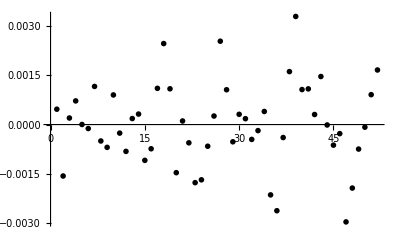

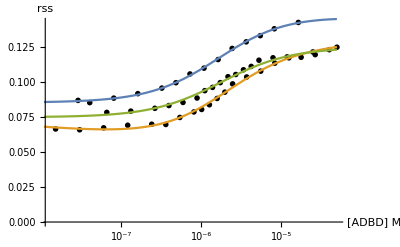

0.0000809323

-2.8171×10^-7

```mathematica
nlmHalfAtsg["BestFitParameters"]
nlmHalfAtsg["ParameterErrors"]
ListPlot[nlmHalfAtsg["FitResiduals"],PlotTheme->"Monochrome"]
Show[ListLogLinearPlot[{HalfTSGMay27A,HalfTSGJune17A,HalfTSGJuly222018A},PlotRange->All,AxesLabel->{"[ADBD] M","rss"}, PlotTheme->"Monochrome"],LogLinearPlot[{halfGREfitModelAtsg[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,mu1,bb2,0,bu2,0,0]/.nlmHalfAtsg["BestFitParameters"],halfGREfitModelAtsg[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,mu1,bb2,0,bu2,0,1]/.nlmHalfAtsg["BestFitParameters"],halfGREfitModelAtsg[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,mu1,bb2,0,bu2,0,2]/.nlmHalfAtsg["BestFitParameters"]},{gr,10^-9,5*10^-5}]]
Total[nlmHalfAtsg["FitResiduals"]^2]
nlmHalfAtsg["ParameterErrors"][[1]]*y/.NMinimize[(0.975-CDF[StudentTDistribution[0
,1
,Length[nlmHalfAtsg["Response"]]-10],x][[2]]/.{x->y})^2
,y][[2]](*95% Conf interval for Kd*)
```

### NLM for C3:

Note that May 4th 2018 data can be fit with or without log bound baseline when on its own. However, in the context of the other datasets, not using a log bound baseline on May 4th yields rather strong systemic residuals and 2x the squared sum of residuals. Caveat: it also moves the Kd to be close to the situation without TSG101cc, so keep in mind.

```mathematica
nlmHalfC3tsg=NonlinearModelFit[globalHalfC3tsg,halfGREfitModelC3tsg[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,0,bb2,mb2,bu2,0,set],{{kd,1*10^-6},{bb0,0.12},{bu0,0.06827558418500337},{bb1,0.12},{bu1,0.06827558418500337},{mb0,0.001},{mb1,0.001},{bb2,0.1},{mb2,0},{bu2,0.03}},{set,gr},MaxIterations->500]
```

FittedModel[Which[set==0,«4»,0.0698037 (1-50000000 (1/100000000+gr+7.16353×10^-7-√(-gr/25000000+(1/(1«7»0)+gr+«22»)^2)))+«1»]]

{kd→7.16353×10^-7,bb0→0.252864,bu0→0.0667025,bb1→0.225287,bu1→0.0675682,mb0→0.0111656,mb1→0.00834597,bb2→0.209826,mb2→0.00813694,bu2→0.0698037}

{1.66119×10^-7,0.00874244,0.000712167,0.0114132,0.000573624,0.000846219,0.00109228,0.0109919,0.000988081,0.000741072}

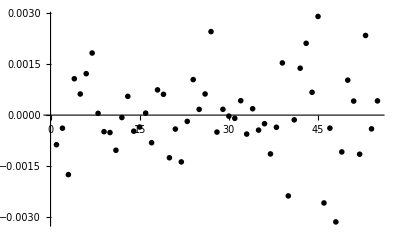

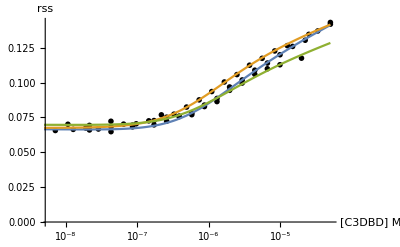

0.0000768737

-3.34581×10^-7

```mathematica
nlmHalfC3tsg["BestFitParameters"]
nlmHalfC3tsg["ParameterErrors"]
ListPlot[nlmHalfC3tsg["FitResiduals"],PlotTheme->"Monochrome"]
Show[ListLogLinearPlot[{HalfTSGccMay8C3,HalfTSGccMay26C3,HalfTSGMay042018C3},PlotRange->All,AxesLabel->{"[C3DBD] M","rss"}, PlotTheme->"Monochrome"],LogLinearPlot[{halfGREfitModelC3tsg[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,0,bb2,mb2,bu2,0,0]/.nlmHalfC3tsg["BestFitParameters"],halfGREfitModelC3tsg[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,0,bb2,mb2,bu2,0,1]/.nlmHalfC3tsg["BestFitParameters"],halfGREfitModelC3tsg[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,0,bb2,mb2,bu2,0,2]/.nlmHalfC3tsg["BestFitParameters"]},{gr,10^-9,5*10^-5}]]
Total[nlmHalfC3tsg["FitResiduals"]^2]
nlmHalfC3tsg["ParameterErrors"][[1]]*y/.NMinimize[(0.975-CDF[StudentTDistribution[0
,1
,Length[nlmHalfC3tsg["Response"]]-10],x][[2]]/.{x->y})^2
,y][[2]](*95% Conf interval for Kd*)
```

## What is the dG of dimerization?

```mathematica
R=1.987; (*cal/K/mol*)
T=293.15;(*K*)
```

```mathematica
dG[kd_]:=-R*T*Log[kd];
```

```mathematica
dG[2.0192053443538756*^-7]-dG[1.33*^-6](*A*)
dG[2.2854895933130998*^-7]-dG[1.58*^-6](*C3*)
```

1098.03

1126.2

Perhaps 1.1 kcal/mol for both A and C3. Multiply by 2 if considering Molar^2 of complex formation.

Could be 2.2 kcal/mol difference if considering two unequal binding sites (1.1 kcal / mol averaged over the two sites):

```mathematica
dG[3*10^-8]-dG[1.33*10^-6](*if ADBD bound in a sequential format, the second site would be 30 nM binding to produce an overall 200 nM observable*)
```

2208.65

If all this energy is going into dimerization, what is the perceived dimerization Kd? (very weak) Worth noting that some of the energy is likely going into conformational rearrangement etc.

```mathematica
Exp[-1126.0/(R*T)]
Exp[-2209.0/(R*T)]
```

0.144701

0.0225427

Intrinsic DNA binding Kd to half-site may be (from EAM of Jing’s paper) *****NOTE THAT OUR EAM ONLY CONSIDERS THE CONFORMATIONAL STATES OF GR, NOT THE DNA. IF DNA WERE CONSIDERED, THEN THE BELOW VALUE WOULD HAVE TO BE LARGER IN MAGNITUDE, AS DNA ALSO GOES THROUGH A CONFORMATIONAL REARRANGEMENT****:

```mathematica
Exp[-(8330.55218096124)/(R*T)]
```

6.14999×10^-7

Calculate conformational work done from difference in binding energies:

```mathematica
dG[6.15*10^-7]-dG[1.33*10^-6](*A using my half-site Kd*)
dG[6.15*10^-7]-dG[1.58*10^-6](*C3*)
```

449.281

549.612

```mathematica
dG[6.15*10^-7]-dG[0.67*10^-6](*A using Jing's half-site Kd*)
dG[6.15*10^-7]-dG[0.91*10^-6](*C3*)
```

49.8934

228.232

XX***Ignore this: Jing’s values indicate the relative work calculated in the original EAM***XX Note that the C3 isoform is pushed into a “DNA binding conformation” (whatever that means) by TSG101cc, while A is not. The ddG of TSG101cc on C3 is ~550 cal / mol; almost exactly the conformational energy expended in C3 binding each half-site of GRE.

The A isoform goes into a dimerization conformation, but binds the half-site better b/c of R-region stabilization. The A isoform work is ~450 cal/mol, and the effect of TSG101cc on full GRE is close (358 ± 46 cal/mol).

### The effect of TSG101 binding A that is binding half site ± errors:

```mathematica
dG[2.047571355796388*^-6+3.67*10^-7]-dG[1.33*10^-6-1.18*10^-7]
dG[2.047571355796388*^-6]-dG[1.33*10^-6]
dG[2.047571355796388*^-6-3.67*10^-7]-dG[1.33*10^-6+1.18*10^-7]
```

-401.481

-251.33

-86.7621

### The effect of TSG101 binding C3 that is binding half site ± errors:

```mathematica
dG[7.163529897490758*^-7+1.66*10^-7]-dG[1.5761007255903991*^-6-6.76*10^-8]
dG[7.163529897490758*^-7]-dG[1.5761007255903991*^-6]
dG[7.163529897490758*^-7-1.66*10^-7]-dG[1.5761007255903991*^-6+6.76*10^-8]
```

312.377

459.314

637.328

## Output Mole Fraction Bound Curves

### Calculate ∂∂G of binding DNA given TSG101

```mathematica
R=1.987;
```

Full-GRE:
A:

```mathematica
nlmFullAmicro["BestFitParameters"]
nlmFullAmicro["ParameterErrors"]
nlmFullTSGccA["BestFitParameters"]
nlmFullTSGccA["ParameterErrors"]
```

{kd→2.12295×10^-7,bb0→0.172987,mb0→0.00408385,bu0→0.0678187,bb1→0.163063,mb1→0.00276632,bu1→0.0699493,bb2→0.120064,bu2→0.0690888,bb3→0.179471,mb3→0.00325025,bu3→0.0947878}

{5.99397×10^-9,0.00529832,0.000401183,0.000530602,0.00490149,0.00039459,0.00066677,0.000643075,0.000518693,0.00480098,0.000369989,0.000484104}

{kd→1.00341×10^-7,bb0→0.181599,mb0→0.00476833,bu0→0.0628844,bb1→0.194361,mb1→0.00475831,bu1→0.110219,bb2→0.206188,mb2→0.00685445,bu2→0.10145,mu1→0.00116485,mu2→0.00157856,bb3→0.195514,mb3→0.00543893,bu3→0.0666228,bb4→0.22094,mb4→0.00704292,bu4→0.0654671}

{4.03335×10^-9,0.00495646,0.000382676,0.000613179,0.00545581,0.000397845,0.00921912,0.00475033,0.0003634,0.0089053,0.000509817,0.000482007,0.00605379,0.00044365,0.00065595,0.00748253,0.000539797,0.00064965}

```mathematica
R*293.15*Log[(1.0034074518173621*^-7-4.0333472276267764*^-9)/(2.1229464080281134*^-7+5.9939731957718526*^-9)]" Fitted values -/+ error"
R*293.15*Log[1.0034074518173621*^-7/2.1229464080281134*^-7]" Fitted values"
R*293.15*Log[(1.0034074518173621*^-7+4.0333472276267764*^-9)/(2.1229464080281134*^-7-5.9939731957718526*^-9)]" Fitted values +/- error"
```

-476.635  Fitted values -/+ error

-436.519  Fitted values

-396.881  Fitted values +/- error

C3:

```mathematica
nlmFullC3micro["BestFitParameters"]
nlmFullC3micro["ParameterErrors"]
nlmFullTSGccC3["BestFitParameters"]
nlmFullTSGccC3["ParameterErrors"]
```

{kd→2.28549×10^-7,bb0→0.20831,mb0→0.00667596,bu0→0.0679305,bb1→0.203589,mb1→0.00583288,bu1→0.0679356,bb2→0.190589,mb2→0.00568312,bu2→0.0911366,mu2→0.00114334}

{1.18321×10^-8,0.0107605,0.000801723,0.000740713,0.0073076,0.000578747,0.000595666,0.0066967,0.000530211,0.00694748,0.00037947}

{kd→9.45453×10^-8,bb0→0.24639,mu0→0.00196024,mb0→0.0101775,bu0→0.0958317,bb1→0.194167,mb1→0.0043946,bu1→0.0752672,bb2→0.212454,mb2→0.00564468,bu2→0.0786822}

{2.54215×10^-9,0.00263751,0.000225704,0.000198549,0.00422923,0.00370724,0.000273787,0.000413885,0.00449928,0.00032502,0.000392164}

```mathematica
R*293.15*(Log[9.454525303745983*^-8-2.5421535588049677*^-9]-Log[2.2854895933130998*^-7+1.1832067567054142*^-8])" Fitted values -/+ error"
R*293.15*(Log[9.454525303745983*^-8]-Log[2.2854895933130998*^-7])" Fitted values"
R*293.15*(Log[9.454525303745983*^-8+2.5421535588049677*^-9]-Log[2.2854895933130998*^-7-1.1832067567054142*^-8])" Fitted values +/- error"
```

-559.424  Fitted values -/+ error

-514.147  Fitted values

-467.727  Fitted values +/- error

#### Half-GRE:

A:

```mathematica
R*293.15*(Log[2.047571355796388*^-6-3.6663229709721203*^-7]-Log[1.3313559028949729*^-6+1.1759399290773822*^-7])"Fitted values -/+ error"
R*293.15*(Log[2.047571355796388*^-6]-Log[1.3313559028949729*^-6])"Fitted values"
R*293.15*(Log[2.047571355796388*^-6+3.6663229709721203*^-7]-Log[1.3313559028949729*^-6-1.1759399290773822*^-7])"Fitted values +/- error"
```

86.5075 Fitted values -/+ error

250.736 Fitted values

400.546 Fitted values +/- error

C3:

```mathematica
R*293.15*(Log[5.985293908378289*^-7-1.1392867866195786*^-7]-Log[1.5761007255903991*^-6+6.760673224468605*^-8])"Fitted values -/+ error"
R*293.15*(Log[5.985293908378289*^-7]-Log[1.5761007255903991*^-6])"Fitted values"
R*293.15*(Log[5.985293908378289*^-7+1.1392867866195786*^-7]-Log[1.5761007255903991*^-6-6.760673224468605*^-8])"Fitted values +/- error"
```

-711.443 Fitted values -/+ error

-563.985 Fitted values

-436.952 Fitted values +/- error

```mathematica
-540.77+291.418
-291.418+95.56318654628035
```

-249.352

-195.855

```mathematica
-942.9126156164853/2
```

-471.456

#### Coupling energy from dimerization (difference between full and half-site GRE’s)

A:

```mathematica
R*293.15*(2*Log[1.3313559028949729*^-6-1.1759399290773822*^-7]-Log[2.0192053461644467*^-7+5.893029553239001*^-8])"Fitted values -/+ error"
R*293.15*(2*Log[1.3313559028949729*^-6]-Log[2.0192053461644467*^-7])"Fitted values"
R*293.15*(2*Log[1.3313559028949729*^-6+1.1759399290773822*^-7]-Log[2.0192053461644467*^-7-5.893029553239001*^-8])"Fitted values +/- error"
```

-7038.95 Fitted values -/+ error

-6782.06 Fitted values

-6482.44 Fitted values +/- error

C3:

```mathematica
R*293.15*(2*Log[1.5761007255903991*^-6-6.760673224468605*^-8]-Log[(4.8873162881444255*^-14)^0.5+7.211314070649369*^-8])"Fitted values -/+ error"
R*293.15*(2*Log[1.5761007255903991*^-6]-Log[(4.8873162881444255*^-14)^0.5])"Fitted values"
R*293.15*(2*Log[1.5761007255903991*^-6+6.760673224468605*^-8]-Log[(4.8873162881444255*^-14)^0.5-7.211314070649369*^-8])"Fitted values +/- error"
```

-6853.76 Fitted values -/+ error

-6638.24 Fitted values

-6359.34 Fitted values +/- error

### A full GRE w/out TSG

```mathematica
globalFullA=Join[FullMarch31A/.{x_,y_}->{0,x,y},
FullApril2A/.{x_,y_}->{1,x,y},
FullApril17A/.{x_,y_}->{2,x,y},
FullMay27A/.{x_,y_}->{3,x,y}];
```

```mathematica
Afrac0[gr_,rss_]:=2*fracGREboundMicro[gr,10^-8,2.1229464080281134*^-7]+2*(rss-(fullGREfitModelAmicro[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,0,bb2,0,bu2,0,bb3,mb3,bu3,0,0]/.nlmFullAmicro["BestFitParameters"]))/(fullGREfitModelAmicro[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,0,bb2,0,bu2,0,bb3,mb3,bu3,0,0]/.nlmFullAmicro["BestFitParameters"]);
```

```mathematica
Afrac1[gr_,rss_]:=2*fracGREbound[gr,10^-8,2.1229464080281134*^-7]+2*(rss-(fullGREfitModelAmicro[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,0,bb2,0,bu2,0,bb3,mb3,bu3,0,1]/.nlmFullAmicro["BestFitParameters"]))/(fullGREfitModelAmicro[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,0,bb2,0,bu2,0,bb3,mb3,bu3,0,1]/.nlmFullAmicro["BestFitParameters"]);
```

```mathematica
Afrac2[gr_,rss_]:=2*fracGREbound[gr,10^-8,2.1229464080281134*^-7]+2*(rss-(fullGREfitModelAmicro[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,0,bb2,0,bu2,0,bb3,mb3,bu3,0,2]/.nlmFullAmicro["BestFitParameters"]))/(fullGREfitModelAmicro[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,0,bb2,0,bu2,0,bb3,mb3,bu3,0,2]/.nlmFullAmicro["BestFitParameters"]);
Afrac3[gr_,rss_]:=2*fracGREbound[gr,10^-8,2.1229464080281134*^-7]+2*(rss-(fullGREfitModelAmicro[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,0,bb2,0,bu2,0,bb3,mb3,bu3,0,3]/.nlmFullAmicro["BestFitParameters"]))/(fullGREfitModelAmicro[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,0,bb2,0,bu2,0,bb3,mb3,bu3,0,3]/.nlmFullAmicro["BestFitParameters"])
```

```mathematica
fracBoundA=Transpose[{Flatten[{Transpose[FullMarch31A][[1]],Transpose[FullApril2A][[1]],Transpose[FullApril17A][[1]],Transpose[FullMay27A][[1]]}],Flatten[{Afrac0[Transpose[FullMarch31A][[1]],Transpose[FullMarch31A][[2]]],Afrac1[Transpose[FullApril2A][[1]],Transpose[FullApril2A][[2]]],Afrac2[Transpose[FullApril17A][[1]],Transpose[FullApril17A][[2]]],Afrac3[Transpose[FullMay27A][[1]],Transpose[FullMay27A][[2]]]}]}];
```

### C3 full GRE w/out TSG

```mathematica
globalFullC3=Join[FullMarch31C3/.{x_,y_}->{0,x,y},
FullApril2C3/.{x_,y_}->{1,x,y},
FullMay8C3/.{x_,y_}->{2,x,y}];
```

```mathematica
C3frac0[gr_,rss_]:=2*fracGREbound[gr,10^-8,2.2854895933130998*^-7]+2*(rss-(fullGREfitModelC3micro[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,0,bb2,mb2,bu2,mu2,0]/.nlmFullC3micro["BestFitParameters"]))/(fullGREfitModelC3micro[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,0,bb2,mb2,bu2,mu2,0]/.nlmFullC3micro["BestFitParameters"]);
```

```mathematica
C3frac1[gr_,rss_]:=2*fracGREbound[gr,10^-8,2.2854895933130998*^-7]+2*(rss-(fullGREfitModelC3micro[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,0,bb2,mb2,bu2,mu2,1]/.nlmFullC3micro["BestFitParameters"]))/(fullGREfitModelC3micro[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,0,bb2,mb2,bu2,mu2,1]/.nlmFullC3micro["BestFitParameters"]);
```

```mathematica
C3frac2[gr_,rss_]:=2*fracGREbound[gr,10^-8,2.2854895933130998*^-7]+2*(rss-(fullGREfitModelC3micro[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,0,bb2,mb2,bu2,mu2,2]/.nlmFullC3micro["BestFitParameters"]))/(fullGREfitModelC3micro[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,0,bb2,mb2,bu2,mu2,2]/.nlmFullC3micro["BestFitParameters"]);
```

```mathematica
fracBoundC3=Transpose[{Flatten[{Transpose[FullMarch31C3][[1]],Transpose[FullApril2C3][[1]],Transpose[FullMay8C3][[1]]}],Flatten[{C3frac0[Transpose[FullMarch31C3][[1]],Transpose[FullMarch31C3][[2]]],C3frac1[Transpose[FullApril2C3][[1]],Transpose[FullApril2C3][[2]]],C3frac2[Transpose[FullMay8C3][[1]],Transpose[FullMay8C3][[2]]]}]}];
```

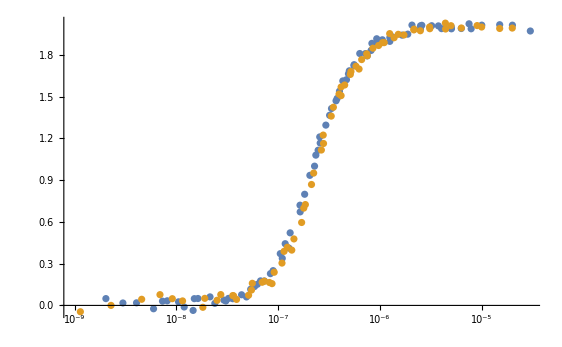

```mathematica
ListLogLinearPlot[{fracBoundA,fracBoundC3}]
```

```mathematica
SetDirectory["~/Documents/My_Research/Hilser_Lab/Steady State Anisotropy/"]
```

/Users/jordanwhite/Documents/My_Research/Hilser_Lab/Steady State Anisotropy

```mathematica
Export["A-GRE_global.csv",N[fracBoundA]]
```

A-GRE_global.csv

```mathematica
Export["C3-GRE_global.csv",N[fracBoundC3]]
```

C3-GRE_global.csv

### A full GRE w/TSG at 100 µM

```mathematica
FullTSGccA=Join[FullTSGApril17A/.{x_,y_}->{0,x,y},
Full2017May26A100/.{x_,y_}->{1,x,y},
FullTSGJune17A/.{x_,y_}->{2,x,y},
Full2018Mar01A100/.{x_,y_}->{3,x,y},
Full2018Mar08A100/.{x_,y_}->{4,x,y}];
```

```mathematica
Atsgfrac0[gr_,rss_]:=2*fracGREboundMicro[gr,10^-8,1.0034074518173621*^-7]+2*(rss-(fullGRETSGfitModelA[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,mu1,bb2,mb2,bu2,mu2,bb3,mb3,bu3,0,bb4,mb4,bu4,0,0]/.nlmFullTSGccA["BestFitParameters"]))/(fullGRETSGfitModelA[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,mu1,bb2,mb2,bu2,mu2,bb3,mb3,bu3,0,bb4,mb4,bu4,0,0]/.nlmFullTSGccA["BestFitParameters"]);
```

```mathematica
Atsgfrac1[gr_,rss_]:=2*fracGREboundMicro[gr,10^-8,1.0034074518173621*^-7]+2*(rss-(fullGRETSGfitModelA[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,mu1,bb2,mb2,bu2,mu2,bb3,mb3,bu3,0,bb4,mb4,bu4,0,1]/.nlmFullTSGccA["BestFitParameters"]))/(fullGRETSGfitModelA[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,mu1,bb2,mb2,bu2,mu2,bb3,mb3,bu3,0,bb4,mb4,bu4,0,1]/.nlmFullTSGccA["BestFitParameters"]);
```

```mathematica
Atsgfrac2[gr_,rss_]:=2*fracGREboundMicro[gr,10^-8,1.0034074518173621*^-7]+2*(rss-(fullGRETSGfitModelA[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,mu1,bb2,mb2,bu2,mu2,bb3,mb3,bu3,0,bb4,mb4,bu4,0,2]/.nlmFullTSGccA["BestFitParameters"]))/(fullGRETSGfitModelA[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,mu1,bb2,mb2,bu2,mu2,bb3,mb3,bu3,0,bb4,mb4,bu4,0,2]/.nlmFullTSGccA["BestFitParameters"]);
Atsgfrac3[gr_,rss_]:=2*fracGREboundMicro[gr,10^-8,1.0034074518173621*^-7]+2*(rss-(fullGRETSGfitModelA[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,mu1,bb2,mb2,bu2,mu2,bb3,mb3,bu3,0,bb4,mb4,bu4,0,3]/.nlmFullTSGccA["BestFitParameters"]))/(fullGRETSGfitModelA[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,mu1,bb2,mb2,bu2,mu2,bb3,mb3,bu3,0,bb4,mb4,bu4,0,3]/.nlmFullTSGccA["BestFitParameters"]);
Atsgfrac4[gr_,rss_]:=2*fracGREboundMicro[gr,10^-8,1.0034074518173621*^-7]+2*(rss-(fullGRETSGfitModelA[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,mu1,bb2,mb2,bu2,mu2,bb3,mb3,bu3,0,bb4,mb4,bu4,0,4]/.nlmFullTSGccA["BestFitParameters"]))/(fullGRETSGfitModelA[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,mu1,bb2,mb2,bu2,mu2,bb3,mb3,bu3,0,bb4,mb4,bu4,0,4]/.nlmFullTSGccA["BestFitParameters"]);
```

```mathematica
fracBoundTSGA=Transpose[{Flatten[{Transpose[FullTSGApril17A][[1]],Transpose[Full2017May26A100][[1]],Transpose[FullTSGJune17A][[1]],Transpose[Full2018Mar01A100][[1]],Transpose[Full2018Mar08A100][[1]]}],Flatten[{Atsgfrac0[Transpose[FullTSGApril17A][[1]],Transpose[FullTSGApril17A][[2]]],Atsgfrac1[Transpose[Full2017May26A100][[1]],Transpose[Full2017May26A100][[2]]],Atsgfrac2[Transpose[FullTSGJune17A][[1]],Transpose[FullTSGJune17A][[2]]],Atsgfrac3[Transpose[Full2018Mar01A100][[1]],Transpose[Full2018Mar01A100][[2]]],Atsgfrac4[Transpose[Full2018Mar08A100][[1]],Transpose[Full2018Mar08A100][[2]]]}]}];
```

### C3 full GRE w/TSG

```mathematica
FullTSGccC3=Join[FullTSGccMay7C3/.{x_,y_}->{0,x,y},
Full2018Mar01C3100/.{x_,y_}->{1,x,y},
Full2018Mar08C3100/.{x_,y_}->{2,x,y}];
```

```mathematica
C3tsgfrac0[gr_,rss_]:=2*fracGREboundMicro[gr,10^-8,9.454525303745983*^-8]+2*(rss-(fullGRETSGfitModelC3[gr,10^-8,kd,bb0,mb0,bu0,mu0,bb1,mb1,bu1,0,bb2,mb2,bu2,0,0]/.nlmFullTSGccC3["BestFitParameters"]))/(fullGRETSGfitModelC3[gr,10^-8,kd,bb0,mb0,bu0,mu0,bb1,mb1,bu1,0,bb2,mb2,bu2,0,0]/.nlmFullTSGccC3["BestFitParameters"]);
```

```mathematica
C3tsgfrac1[gr_,rss_]:=2*fracGREboundMicro[gr,10^-8,9.454525303745983*^-8]+2*(rss-(fullGRETSGfitModelC3[gr,10^-8,kd,bb0,mb0,bu0,mu0,bb1,mb1,bu1,0,bb2,mb2,bu2,0,1]/.nlmFullTSGccC3["BestFitParameters"]))/(fullGRETSGfitModelC3[gr,10^-8,kd,bb0,mb0,bu0,mu0,bb1,mb1,bu1,0,bb2,mb2,bu2,0,1]/.nlmFullTSGccC3["BestFitParameters"]);
C3tsgfrac2[gr_,rss_]:=2*fracGREboundMicro[gr,10^-8,9.454525303745983*^-8]+2*(rss-(fullGRETSGfitModelC3[gr,10^-8,kd,bb0,mb0,bu0,mu0,bb1,mb1,bu1,0,bb2,mb2,bu2,0,2]/.nlmFullTSGccC3["BestFitParameters"]))/(fullGRETSGfitModelC3[gr,10^-8,kd,bb0,mb0,bu0,mu0,bb1,mb1,bu1,0,bb2,mb2,bu2,0,2]/.nlmFullTSGccC3["BestFitParameters"]);
```

```mathematica
fracBoundTSGC3=Transpose[{Flatten[{Transpose[FullTSGccMay7C3][[1]],Transpose[Full2018Mar01C3100][[1]],Transpose[Full2018Mar08C3100][[1]]}],Flatten[{C3tsgfrac0[Transpose[FullTSGccMay7C3][[1]],Transpose[FullTSGccMay7C3][[2]]],C3tsgfrac1[Transpose[Full2018Mar01C3100][[1]],Transpose[Full2018Mar01C3100][[2]]],C3tsgfrac2[Transpose[Full2018Mar08C3100][[1]],Transpose[Full2018Mar08C3100][[2]]]}]}];
```

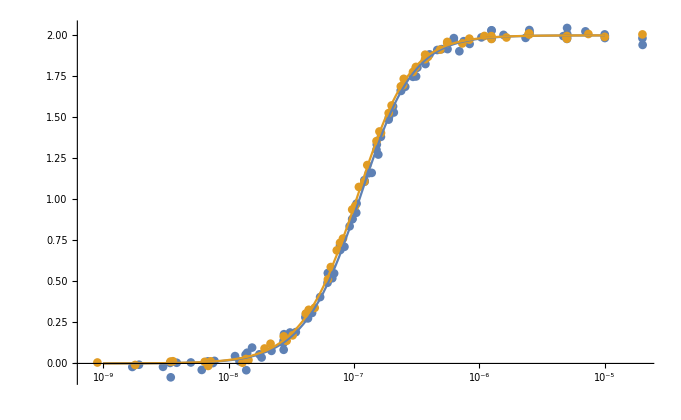

```mathematica
Show[ListLogLinearPlot[{fracBoundTSGA,fracBoundTSGC3}],LogLinearPlot[{2*fracGREboundMicro[gr,10^-8,1.0034074518173621*^-7],2*fracGREboundMicro[gr,10^-8,0.94545*^-7]},{gr,10^-9,10^-5}]]
```

```mathematica
Export["A-GRE+TSG_global.csv",N[fracBoundTSGA]]
```

A-GRE+TSG_global.csv

```mathematica
Export["C3-GRE+TSG_global.csv",N[fracBoundTSGC3]]
```

C3-GRE+TSG_global.csv

### A half GRE w/out TSG

```mathematica
Ahalffrac0[gr_,rss_]:=fracHalfSiteBound[gr,10^-8,1.3313559028949729*^-6]+(rss-(halfGREfitModelA[gr,10^-8,kd,bb0,0,bu0,0,bb1,0,bu1,0,bb2,0,bu2,0,0]/.nlmHalfA["BestFitParameters"]))/(halfGREfitModelA[gr,10^-8,kd,bb0,0,bu0,0,bb1,0,bu1,0,bb2,0,bu2,0,0]/.nlmHalfA["BestFitParameters"]);
Ahalffrac1[gr_,rss_]:=fracHalfSiteBound[gr,10^-8,1.3313559028949729*^-6]+(rss-(halfGREfitModelA[gr,10^-8,kd,bb0,0,bu0,0,bb1,0,bu1,0,bb2,0,bu2,0,1]/.nlmHalfA["BestFitParameters"]))/(halfGREfitModelA[gr,10^-8,kd,bb0,0,bu0,0,bb1,0,bu1,0,bb2,0,bu2,0,1]/.nlmHalfA["BestFitParameters"]);
Ahalffrac2[gr_,rss_]:=fracHalfSiteBound[gr,10^-8,1.3313559028949729*^-6]+(rss-(halfGREfitModelA[gr,10^-8,kd,bb0,0,bu0,0,bb1,0,bu1,0,bb2,0,bu2,0,2]/.nlmHalfA["BestFitParameters"]))/(halfGREfitModelA[gr,10^-8,kd,bb0,0,bu0,0,bb1,0,bu1,0,bb2,0,bu2,0,2]/.nlmHalfA["BestFitParameters"]);
```

```mathematica
fracBoundHalfA=Transpose[{Flatten[{Transpose[HalfApril1A][[1]],Transpose[HalfApril3A][[1]],Transpose[HalfJune17A][[1]]}],Flatten[{Ahalffrac0[Transpose[HalfApril1A][[1]],Transpose[HalfApril1A][[2]]],Ahalffrac1[Transpose[HalfApril3A][[1]],Transpose[HalfApril3A][[2]]],
Ahalffrac2[Transpose[HalfJune17A][[1]],Transpose[HalfJune17A][[2]]]}]}];
```

### C3 half GRE w/out TSG

```mathematica
C3halffrac0[gr_,rss_]:=fracHalfSiteBound[gr,10^-8,1.5761007255903991*^-6]+(rss-(halfGREfitModelC3[gr,10^-8,kd,bb0,mb0,bu0,mu0,bb1,0,bu1,0,bb2,mb2,bu2,mu2,bb3,0,bu3,0,0]/.nlmHalfC3["BestFitParameters"]))/(halfGREfitModelC3[gr,10^-8,kd,bb0,mb0,bu0,mu0,bb1,0,bu1,0,bb2,mb2,bu2,mu2,bb3,0,bu3,0,0]/.nlmHalfC3["BestFitParameters"]);
C3halffrac1[gr_,rss_]:=fracHalfSiteBound[gr,10^-8,1.5761007255903991*^-6]+(rss-(halfGREfitModelC3[gr,10^-8,kd,bb0,mb0,bu0,mu0,bb1,0,bu1,0,bb2,mb2,bu2,mu2,bb3,0,bu3,0,1]/.nlmHalfC3["BestFitParameters"]))/(halfGREfitModelC3[gr,10^-8,kd,bb0,mb0,bu0,mu0,bb1,0,bu1,0,bb2,mb2,bu2,mu2,bb3,0,bu3,0,1]/.nlmHalfC3["BestFitParameters"]);
C3halffrac2[gr_,rss_]:=fracHalfSiteBound[gr,10^-8,1.5761007255903991*^-6]+(rss-(halfGREfitModelC3[gr,10^-8,kd,bb0,mb0,bu0,mu0,bb1,0,bu1,0,bb2,mb2,bu2,mu2,bb3,0,bu3,0,2]/.nlmHalfC3["BestFitParameters"]))/(halfGREfitModelC3[gr,10^-8,kd,bb0,mb0,bu0,mu0,bb1,0,bu1,0,bb2,mb2,bu2,mu2,bb3,0,bu3,0,2]/.nlmHalfC3["BestFitParameters"]);
C3halffrac3[gr_,rss_]:=fracHalfSiteBound[gr,10^-8,1.5761007255903991*^-6]+(rss-(halfGREfitModelC3[gr,10^-8,kd,bb0,mb0,bu0,mu0,bb1,0,bu1,0,bb2,mb2,bu2,mu2,bb3,0,bu3,0,3]/.nlmHalfC3["BestFitParameters"]))/(halfGREfitModelC3[gr,10^-8,kd,bb0,mb0,bu0,mu0,bb1,0,bu1,0,bb2,mb2,bu2,mu2,bb3,0,bu3,0,3]/.nlmHalfC3["BestFitParameters"]);
```

```mathematica
fracBoundHalfC3=Transpose[{Flatten[{Transpose[HalfApril1C3][[1]],Transpose[HalfApril3C3][[1]],Transpose[HalfMay8C3][[1]],Transpose[HalfMay26C3][[1]]}],Flatten[{C3halffrac0[Transpose[HalfApril1C3][[1]],Transpose[HalfApril1C3][[2]]],C3halffrac1[Transpose[HalfApril3C3][[1]],Transpose[HalfApril3C3][[2]]],
C3halffrac2[Transpose[HalfMay8C3][[1]],Transpose[HalfMay8C3][[2]]],
C3halffrac3[Transpose[HalfMay26C3][[1]],Transpose[HalfMay26C3][[2]]]}]}];
```

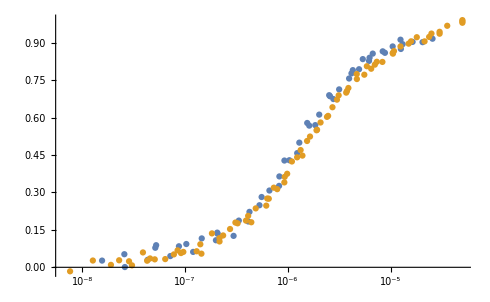

```mathematica
ListLogLinearPlot[{fracBoundHalfA,fracBoundHalfC3}]
```

```mathematica
Export["A-halfGRE_global.csv",N[fracBoundHalfA]]
```

A-halfGRE_global.csv

```mathematica
Export["C3-halfGRE_global.csv",N[fracBoundHalfC3]]
```

C3-halfGRE_global.csv

### A half GRE w/TSG

```mathematica
nlmHalfAtsg["BestFitParameters"]
```

{kd→1.76058×10^-6,bb0→0.135958,bu0→0.0852151,bb1→0.139146,bu1→0.0314035,mb0→-0.00111014,mb1→0.00117401,mu1→-0.00197858,bb2→0.124664,bu2→0.0747791}

```mathematica
AhalffracTSG0[gr_,rss_]:=fracHalfSiteBound[gr,10^-8,1.7605839183499407*^-6]+(rss-(halfGREfitModelAtsg[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,mu1,bb2,0,bu2,0,0]/.nlmHalfAtsg["BestFitParameters"]))/(halfGREfitModelAtsg[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,mu1,bb2,0,bu2,0,0]/.nlmHalfAtsg["BestFitParameters"]);
AhalffracTSG1[gr_,rss_]:=fracHalfSiteBound[gr,10^-8,1.7605839183499407*^-6]+(rss-(halfGREfitModelAtsg[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,mu1,bb2,0,bu2,0,1]/.nlmHalfAtsg["BestFitParameters"]))/(halfGREfitModelAtsg[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,mu1,bb2,0,bu2,0,1]/.nlmHalfAtsg["BestFitParameters"]);
AhalffracTSG2[gr_,rss_]:=fracHalfSiteBound[gr,10^-8,1.7605839183499407*^-6]+(rss-(halfGREfitModelAtsg[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,mu1,bb2,0,bu2,0,2]/.nlmHalfAtsg["BestFitParameters"]))/(halfGREfitModelAtsg[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,mu1,bb2,0,bu2,0,2]/.nlmHalfAtsg["BestFitParameters"]);
```

```mathematica
fracBoundHalfAtsg=Transpose[{Flatten[{Transpose[HalfTSGMay27A][[1]],Transpose[HalfTSGJune17A][[1]],Transpose[HalfTSGJuly222018A][[1]]}],Flatten[{AhalffracTSG0[Transpose[HalfTSGMay27A][[1]],Transpose[HalfTSGMay27A][[2]]],AhalffracTSG1[Transpose[HalfTSGJune17A][[1]],Transpose[HalfTSGJune17A][[2]]],
AhalffracTSG2[Transpose[HalfTSGJuly222018A][[1]],Transpose[HalfTSGJuly222018A][[2]]]}]}];
```

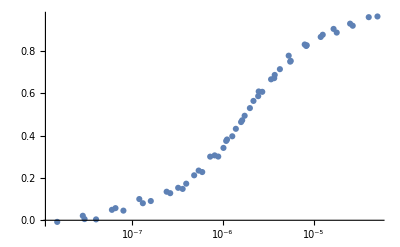

```mathematica
ListLogLinearPlot[{fracBoundHalfAtsg}]
```

### C3 half GRE w/TSG

```mathematica
C3halffracTSG0[gr_,rss_]:=fracHalfSiteBound[gr,10^-8,7.163529897490758*^-7]+(rss-(halfGREfitModelC3tsg[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,0,bb2,mb2,bu2,0,0]/.nlmHalfC3tsg["BestFitParameters"]))/(halfGREfitModelC3tsg[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,0,bb2,mb2,bu2,0,0]/.nlmHalfC3tsg["BestFitParameters"]);
C3halffracTSG1[gr_,rss_]:=fracHalfSiteBound[gr,10^-8,7.163529897490758*^-7]+(rss-(halfGREfitModelC3tsg[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,0,bb2,mb2,bu2,0,1]/.nlmHalfC3tsg["BestFitParameters"]))/(halfGREfitModelC3tsg[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,0,bb2,mb2,bu2,0,1]/.nlmHalfC3tsg["BestFitParameters"]);
C3halffracTSG2[gr_,rss_]:=fracHalfSiteBound[gr,10^-8,7.163529897490758*^-7]+(rss-(halfGREfitModelC3tsg[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,0,bb2,mb2,bu2,0,2]/.nlmHalfC3tsg["BestFitParameters"]))/(halfGREfitModelC3tsg[gr,10^-8,kd,bb0,mb0,bu0,0,bb1,mb1,bu1,0,bb2,mb2,bu2,0,2]/.nlmHalfC3tsg["BestFitParameters"]);
```

```mathematica
fracBoundHalfC3tsg=Transpose[{Flatten[{Transpose[HalfTSGccMay8C3][[1]],Transpose[HalfTSGccMay26C3][[1]],Transpose[HalfTSGMay042018C3][[1]]}],Flatten[{C3halffracTSG0[Transpose[HalfTSGccMay8C3][[1]],Transpose[HalfTSGccMay8C3][[2]]],C3halffracTSG1[Transpose[HalfTSGccMay26C3][[1]],Transpose[HalfTSGccMay26C3][[2]]],C3halffracTSG2[Transpose[HalfTSGMay042018C3][[1]],Transpose[HalfTSGMay042018C3][[2]]]}]}];
```

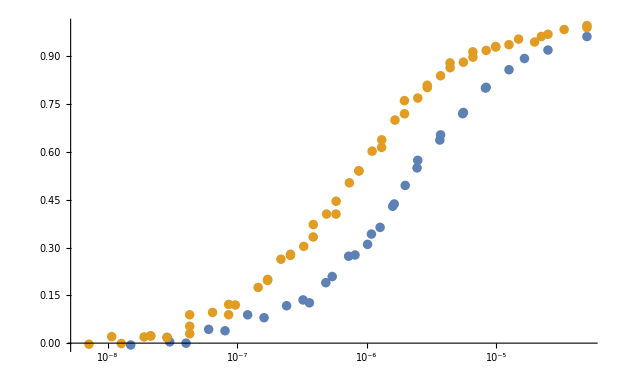

```mathematica
ListLogLinearPlot[{fracBoundHalfAtsg,fracBoundHalfC3tsg}]
```

```mathematica
SetDirectory["~/Documents/My_Research/Hilser_Lab/Steady State Anisotropy/"]
```

/Users/jordanwhite/Documents/My_Research/Hilser_Lab/Steady State Anisotropy

```mathematica
Export["A-halfGRE_global_TSG.csv",N[fracBoundHalfAtsg]]
```

A-halfGRE_global_TSG.csv

```mathematica
Export["C3-halfGRE_global_TSG.csv",N[fracBoundHalfC3tsg]]
```

C3-halfGRE_global_TSG.csv

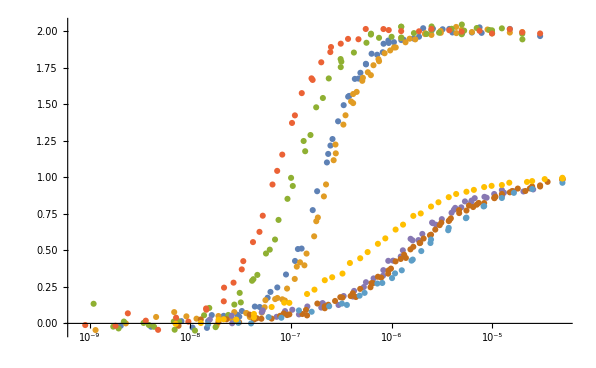

```mathematica
ListLogLinearPlot[{fracBoundA,fracBoundC3,fracBoundTSGA,fracBoundTSGC3,fracBoundHalfA,fracBoundHalfC3,fracBoundHalfAtsg,fracBoundHalfC3tsg}]
```

```mathematica
a=Transpose[{Table[10^x,{x,-9,-4.3,0.05}],2*fracGREbound[Table[10^x,{x,-9,-4.3,0.05}],10^-8,3.6502249155028246*^-14]}];
c3=Transpose[{Table[10^x,{x,-9,-4.3,0.05}],2*fracGREbound[Table[10^x,{x,-9,-4.3,0.05}],10^-8,5.223462841499177*^-14]}];
aTSG=Transpose[{Table[10^x,{x,-9,-4.3,0.05}],2*fracGREbound[Table[10^x,{x,-9,-4.3,0.05}],10^-8,9.669545071842826*^-15]}];
c3TSG=Transpose[{Table[10^x,{x,-9,-4.3,0.05}],2*fracGREbound[Table[10^x,{x,-9,-4.3,0.05}],10^-8,3.584067020074381*^-15]}];
aHalf=Transpose[{Table[10^x,{x,-9,-4.3,0.05}],fracHalfSiteBound[Table[10^x,{x,-9,-4.3,0.05}],10^-8,1.3313559028949729*^-6]}];
c3Half=Transpose[{Table[10^x,{x,-9,-4.3,0.05}],fracHalfSiteBound[Table[10^x,{x,-9,-4.3,0.05}],10^-8,1.5761007255903991*^-6]}];
aHalfTSG=Transpose[{Table[10^x,{x,-9,-4.3,0.05}],fracHalfSiteBound[Table[10^x,{x,-9,-4.3,0.05}],10^-8,2.047571355796388*^-6]}];
c3HalfTSG=Transpose[{Table[10^x,{x,-9,-4.3,0.05}],fracHalfSiteBound[Table[10^x,{x,-9,-4.3,0.05}],10^-8,5.985293908378289*^-7]}];
```

```mathematica
Export["a-fit_GRE.csv",a]
Export["c3-fit_GRE.csv",c3]
Export["aTSG-fit_GRE.csv",aTSG]
Export["c3TSG-fit_GRE.csv",c3TSG]
Export["a-fit_halfGRE.csv",aHalf]
Export["c3-fit_halfGRE.csv",c3Half]
Export["aTSG-fit_halfGRE.csv",aHalfTSG]
Export["c3TSG-fit_halfGRE.csv",c3HalfTSG]
```

a-fit_GRE.csv

c3-fit_GRE.csv

aTSG-fit_GRE.csv

c3TSG-fit_GRE.csv

a-fit_halfGRE.csv

c3-fit_halfGRE.csv

aTSG-fit_halfGRE.csv

c3TSG-fit_halfGRE.csv